# Numerical IST For Infinite Order Rogue Waves

Copyright Deniz Bilman 2018.

This notebook computes the special solution of the nonlinear Schrodinger equation that is the large order limit of fundamental rogue waves studied in the article 
D. Bilman, L. Ling, P. Miller, Extreme Superposition: Rogue Waves of Infinite Order and The Painlevé III Hierarchy, 2018.

The modules require RHPackage (http://www.maths.usyd.edu.au/u/olver/projects/RHPackage.html) and ISTPackage (https://bitbucket.org/trogdon/istpackage).

```mathematica
AppendTo[$Path,"~/RHPackage"];
AppendTo[$Path,"~/ISTPackage"];
<<RiemannHilbert`;
<<ISTPackage`;
```

```mathematica
SetDirectory[NotebookDirectory[]]
$Assumptions={Element[x,Reals],Element[t,Reals],Element[X,Reals],Element[T,Reals]};
LargeQ[z_]:=(Abs[z]>100000);
meps=$MachineEpsilon;
RHSolved[X_]:=RHSolved[X]=RHSolve[X];
RHSolved[{}]:=0.;
```

/Users/bilman/Dropbox/rogue-waves

```mathematica
(* Resolving ListPlot's PlotMarker location problem: *)
marker[prim_,opts___][in_: ColorData[97,"ColorList"][[1]],out_:ColorData[97,"ColorList"][[1]],size_: 9]:=Graphics[{in,prim},opts,ImageSize->size]
square=marker@Rectangle[];
circle=marker@Disk[];
diamond=marker@Polygon[{{0,1},{1,2},{2,1},{1,0}}];
triangle=marker[Polygon[{{1,0},{0,Sqrt[3]},{-1,0}}],AlignmentPoint->{0,1/Sqrt[3]}];
(* Use "circle[]". See the example below: *)
(*ListLinePlot[somedata,PlotMarkers-> circle[]]*)
```

## Contour Truncation Modules for Line Segment Contours -- used in all regions

Calls the TruncateMatrix routine from the ISTPackage .

```mathematica
numptsmax=160;
numptsmin=40;
trunctol=10^(-13);
TruncatedLineContoursv0[jump_,points_,numptsmax_,numptsmin_][X_]:=Module[{jumplist={},j,domx,numpts,linlen,nn},
j=1;
While[j<Length[points],domx=TruncateMatrix[trunctol][{jump[X,0.][#]/.Underflow[]->0./.Indeterminate[]->1.&,Line[{points[[j]],points[[j+1]]}],numptsmax}];
If[domx≠{},linlen=Abs[points[[j]]-points[[j+1]]];nn=Abs[domx[[1]][[1]][[2]]-domx[[1]][[1]][[1]]];numpts=Round[nn/linlen*numptsmax];
Print[Max[numptsmin,numpts]];
AppendTo[jumplist,Fun[jump[X,0][#]&,domx[[1]],Max[numptsmin,numpts]]];];
j=j+1;
];
Return[jumplist];
];
TruncatedLineContours[jump_,points_,numptsmax_,numptsmin_][X_,v_]:=Module[{jumplist={},j,domx,numpts,linlen,nn},
j=1;
While[j<Length[points],
domx=TruncateMatrix[trunctol][{jump[X,v][#]/.Underflow[]->0.&,Line[{points[[j]],points[[j+1]]}],numptsmax}];
If[domx≠{},linlen=Abs[points[[j]]-points[[j+1]]];
nn=Abs[domx[[1]][[1]][[2]]-domx[[1]][[1]][[1]]];
numpts=Round[nn/linlen*numptsmax];
Print[Max[numptsmin,numpts]];
AppendTo[jumplist,Fun[jump[X,v][#]&,domx[[1]],Max[numptsmin,numpts]]];];
j=j+1;
];
Return[jumplist];
];
```

# The Original Big Circle RHP in (X,T)-coordinates RHP 4 in the manuscript

```mathematica
Clear[JumpOriginalCircle];
circrad=0.8;
origpoints=120;
Q=(1/Sqrt[2]){{1,-1},{1,1}};
Qi=Transpose[Q];
ExpMat[X_,T_][z_]:=DiagonalMatrix[{Exp[-I(z X + z^2 T+2/z)],Exp[I(z X + z^2 T+2/z)]}];
ExpMati[X_,T_][z_]:=DiagonalMatrix[{Exp[I(z X + z^2 T+2/z)],Exp[-I(z X + z^2 T+2/z)]}];
(*The core of the jump for the limiting RHP as n -> ∞ is Inverse[Q]=Transpose[Q]*)
JmatCircle[X_,T_][z_]:=ExpMat[X,T][z].Qi.ExpMati[X,T][z];
JumpOriginalCircle[rcirc_][X_,T_]:={Fun[JmatCircle[X,T][#]&,Arc[0.,rcirc,{Pi,0}],origpoints],Fun[JmatCircle[X,T][#]&,Arc[0.,rcirc,{0,-Pi}],origpoints]};

RHOrigSol[rcirc_][X_,T_]:=RHOrigSol[rcirc][X,T]=-((RHSolved[JumpOriginalCircle[rcirc][X,T]])//DomainIntegrate)/(Pi);
nlsOrig[rcirc_][X_,T_]:=RHOrigSol[rcirc][X,T][[1,2]];
```

{{1/(√2),ⅇ^(-8 ⅈ)/(√2)},{-ⅇ^(8 ⅈ)/(√2),1/(√2)}}

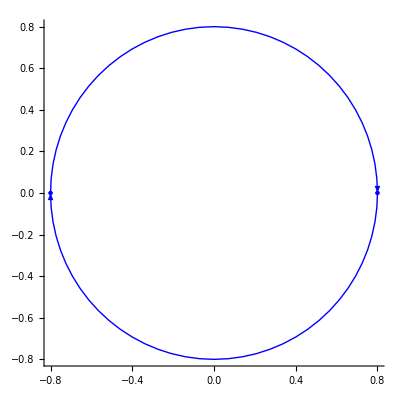

((1. | 0
0 | 1.) | -0.8
(1. | 0
0 | 1.) | 0.8)

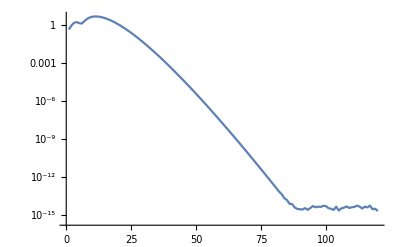
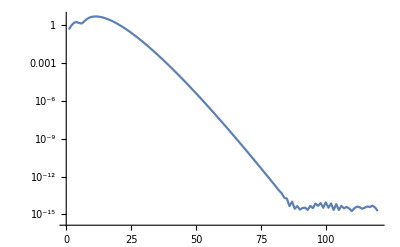

```mathematica
JmatCircle[1,1][1]
JumpOriginalCircle[circrad][1,1]//DomainPlot
JumpOriginalCircle[circrad][1,1]//mRHWellPosed
solorig=RHSolved[JumpOriginalCircle[circrad][1.,0.25]];
DCTPlot/@solorig
```

# Large-X deformation of RHP 4 (parabolic cylinder parametrices)

## R-RHP for large X, small v: 0≤v<54^(-1/2). v is time rescaled: T = v*|X|^(3/2)

```mathematica
(* v is time rescaled: T = v |X|^{3/2} *)
(*We know the potential ψ[X,T]=ψ[-X,T] for all T so σ=1 is enough to consider.*)
σ=1;
ϕ[X_,v_][z_]:=Sqrt[Abs[X]]*(σ*z+v*z^2+2/z);
JumpNoDeform[X_,v_][z_]:=DiagonalMatrix[{Exp[-I ϕ[X,v][z]],Exp[I ϕ[X,v][z]]}].Qi.DiagonalMatrix[{Exp[I ϕ[X,v][z]],Exp[-I ϕ[X,v][z]]}];
```

## Matrix factorizations for small v

Factorization check: Must get the identity matrix

{{1,0},{0,1}}

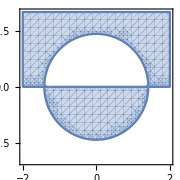

```mathematica
(*Nonstandard Factorization*)
vfun[X_,T_]:=T/X^((3/2));
wcrit=54^(1/3);
Xcrit[T_]:=wcrit*T^(2/3);
Pmat[X_,v_][z_]:={{1,0},{-Exp[2I ϕ[X,v][z]],1}};
Pmati[X_,v_][z_]:={{1,0},{Exp[2I ϕ[X,v][z]],1}};
Mmat[X_,v_][z_]:={{1,(1/2)*Exp[-2I ϕ[X,v][z]]},{0,1}};
Mmati[X_,v_][z_]:={{1,-(1/2)*Exp[-2I ϕ[X,v][z]]},{0,1}};
Lmat[X_,v_][z_]:={{1,0},{(-1/2)Exp[2I ϕ[X,v][z]],1}};
Lmati[X_,v_][z_]:={{1,0},{(1/2)Exp[2I ϕ[X,v][z]],1}};
Umat[X_,v_][z_]:={{1,Exp[-2I ϕ[X,v][z]]},{0,1}};
Umati[X_,v_][z_]:={{1,-Exp[-2I ϕ[X,v][z]]},{0,1}};
Dmat[X_,v_][z_]:=DiagonalMatrix[{2,1/2}];
Dmati[X_,v_][z_]:=DiagonalMatrix[{1/2,2}];
Print["Factorization check: Must get the identity matrix"]
Inverse[Umat[X,v][z]].Lmati[X,v][z].Dmat[X,v][z].Mmat[X,v][z].Pmat[X,v][z]//FullSimplify
RegionPlot[Im[ϕ[1,0][a+I b]]>0,{a,-2,2},{b,-2,2},ImageSize->Small]
```

## Jump matrices and contours for v=0

### Stationary phase points asmall=asmall[v] and bsmall=bsmall[v] for small v>0 and Line Segment Jump Contours

```mathematica
Clear[z0]
z0[v_]:=Roots[z^2+2 v z^3-2==0,z];

a0=-Sqrt[2]//N; b0=Sqrt[2]//N;
rad=b0/Cos[Pi/4]//N;
rbig=2.;
rsmall=0.5 ;
numpointsout=120;
numpointsin=80;
ptsUHPoutv0={a0,a0-rbig(1-I),rbig *b0* I,b0+rbig(1+I),b0};
ptsLHPoutv0=-ptsUHPoutv0;
ptsUHPinv0={a0,a0+rsmall(1+I),b0+rsmall(-1+I),b0};
ptsLHPinv0=-ptsUHPinv0;
ptsLHPcirc={b0,b0-I,-I b0,a0-I,a0};
JumpsLinesXv0[X_]:={Fun[Pmat[X,0][#]&,Line[{ptsUHPoutv0[[1]],ptsUHPoutv0[[2]]}],numpointsout],Fun[Pmat[X,0][#]&,Line[{ptsUHPoutv0[[2]],ptsUHPoutv0[[3]]}],numpointsout],Fun[Pmat[X,0][#]&,Line[{ptsUHPoutv0[[3]],ptsUHPoutv0[[4]]}],numpointsout],Fun[Pmat[X,0][#]&,Line[{ptsUHPoutv0[[4]],ptsUHPoutv0[[5]]}],numpointsin],Fun[Mmat[X,0][#]&,Line[{ptsUHPinv0[[1]],ptsUHPinv0[[2]]}],numpointsin],Fun[Mmat[X,0][#]&,Line[{ptsUHPinv0[[2]],ptsUHPinv0[[3]]}],numpointsin],Fun[Mmat[X,0][#]&,Line[{ptsUHPinv0[[3]],ptsUHPinv0[[4]]}],numpointsin],Fun[Lmat[X,0][#]&,Line[{ptsLHPinv0[[1]],ptsLHPinv0[[2]]}],numpointsin],Fun[Lmat[X,0][#]&,Line[{ptsLHPinv0[[2]],ptsLHPinv0[[3]]}],numpointsin],Fun[Lmat[X,0][#]&,Line[{ptsLHPinv0[[3]],ptsLHPinv0[[4]]}],numpointsin],Fun[Umat[X,0][#]&,Line[{ptsLHPoutv0[[1]],ptsLHPoutv0[[2]]}],numpointsout],
Fun[Umat[X,0][#]&,Line[{ptsLHPoutv0[[2]],ptsLHPoutv0[[3]]}],numpointsout],Fun[Umat[X,0][#]&,Line[{ptsLHPoutv0[[3]],ptsLHPoutv0[[4]]}],numpointsout],Fun[Umat[X,0][#]&,Line[{ptsLHPoutv0[[4]],ptsLHPoutv0[[5]]}],numpointsout],Fun[Dmat[X,0][#]&,Line[{a0,b0}],numpointsin]};
(*JumpsLinesXv0[400]//DomainPlot
JumpsLinesXv0[400]//mRHWellPosed//N*)
```

#### Contour truncation for v=0

40

40

71

72

71

72

40

40

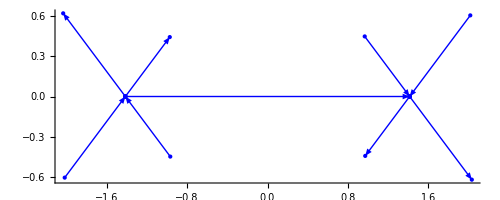

```mathematica
numptsmax=80;
numptsmin=40;
JumpsTruncLinesXv0[X_]:=Join[TruncatedLineContoursv0[Pmat,ptsUHPoutv0,numptsmax,numptsmin][X],TruncatedLineContoursv0[Mmat,ptsUHPinv0,numptsmax,numptsmin][X],TruncatedLineContoursv0[Lmat,ptsLHPinv0,numptsmax,numptsmin][X],TruncatedLineContoursv0[Umat,ptsLHPoutv0,numptsmax,numptsmin][X],{Fun[Dmat[X,0][#]&,Line[{a0,b0}],numpointsin]}];
Xtest=2000;
JumpsTruncLinesXv0[Xtest]//DomainPlot
(*JumpsTruncLinesXv0[Xtest]//mRHWellPosed//N
solXv0=RHSolved[JumpsTruncLinesXv0[Xtest]];
DCTPlot/@solXv0*)
```

## Compute Solution for v=0 Without Contour Truncation

#### Setup

```mathematica
RHLinesSolXv0[X_]:=RHLinesSolXv0[X]=-((RHSolved[JumpsLinesXv0[X]])//DomainIntegrate)/(Pi);
nlsLinesXv0[X_]:=Piecewise[{{4.0,X==0},{RHLinesSolXv0[X][[1,2]]/Sqrt[X],True}}];
rhpgridsize=0.1;
XL=2000.;
XR=2000.3;
rhpxgrid=Table[xx,{xx,XL,XR,rhpgridsize}];
```

#### Execute - Not Used in Practice.

```mathematica
nlsTableXv0=Monitor[Table[nlsLinesXv0[X],{X,XL,XR,rhpgridsize}],X];
nlsReFunXv0=Interpolation[Transpose@{rhpxgrid,Re[nlsTableXv0]}];
nlsImFunXv0=Interpolation[Transpose@{rhpxgrid,Im[nlsTableXv0]}];
ψXv0[X_]:=Piecewise[{{nlsReFunXv0[X]+I*nlsImFunXv0[X],X≥0},{nlsReFunXv0[X]+I*nlsImFunXv0[X],X<0}}];
```

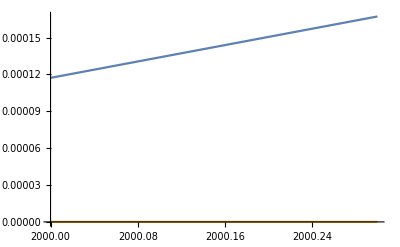

```mathematica
Plot[{Re[ψXv0[X]],Im[ψXv0[X]]},{X,XL,XR},PlotRange->All]
```

## Compute Solution for v=0 With Contour Truncation -- much faster

#### Setup

```mathematica
RHTruncLinesSolXv0[X_]:=RHTruncLinesSolXv0[X]=-((RHSolved[JumpsTruncLinesXv0[X]])//DomainIntegrate)/(Pi);
nlsTruncLinesXv0[X_]:=Piecewise[{{4.0,X==0},{RHTruncLinesSolXv0[X][[1,2]]/Sqrt[X],True}}];
rhpgridsize=0.1;
XL=2000.;
XR=2000.3;
rhpxgrid=Table[xx,{xx,XL,XR,rhpgridsize}];
```

#### Execute - Not used in practice.

```mathematica
(*RHSolved[X_]:=RHSolved[X]=RHSolve[X];RHSolved[{}]:=0.;*)
nlsTruncTableXv0=Monitor[Table[nlsTruncLinesXv0[X],{X,XL,XR,rhpgridsize}],X];
nlsTruncReFunXv0=Interpolation[Transpose@{rhpxgrid,Re[nlsTruncTableXv0]}];
nlsTruncImFunXv0=Interpolation[Transpose@{rhpxgrid,Im[nlsTruncTableXv0]}];
ψtruncXv0[X_]:=Piecewise[{{nlsTruncReFunXv0[X]+I*nlsTruncImFunXv0[X],X≥0},{nlsTruncReFunXv0[X]+I*nlsTruncImFunXv0[X],X<0}}];
```

```mathematica
Plot[{Re[ψtruncXv0[X]],Im[ψtruncXv0[X]]},{X,XL,XR}]
```

-Graphics-

## Jump matrices for general 0≤v<54^(-1/2)

```mathematica
Clear[av];Clear[bv];
av[v_/;0≤ v<1/Sqrt[54]]:=(-Sqrt[2]//N)/;v==0.;
bv[v_/;0≤ v<1/Sqrt[54]]:=(Sqrt[2]//N)/;v==0.;
av[v_/;0≤ v<1/Sqrt[54]]:=List@@z0[v][[All,2]][[2]]/;v>0.;
bv[v_/;0≤ v<1/Sqrt[54]]:=List@@z0[v][[All,2]][[3]]/;v>0.;
rbig=2.;
rsmall=0.5 ;
numpointsout=120;
numpointsin=80;
ptsUHPout[v_]:={av[v],av[v]+rbig(-1+I),rbig *Max[Abs[av[v]],Abs[bv[v]]]* I,bv[v]+rbig(1+I),bv[v]};
ptsLHPout[v_]:={bv[v],bv[v]+rbig(1-I),-rbig*Max[Abs[av[v]],Abs[bv[v]]]* I,av[v]+rbig(-1-I),av[v]};
ptsUHPin[v_]:={av[v],av[v]+rsmall(1+I),bv[v]+rsmall(-1+I),bv[v]};
ptsLHPin[v_]:={bv[v],bv[v]+rsmall(-1-I),av[v]+rsmall(1-I),av[v]};
JumpsLinesX[X_,v_/;v<1/Sqrt[54]]:={Fun[Pmat[X,v][#]&,Line[{ptsUHPout[v][[1]],ptsUHPout[v][[2]]}],numpointsout],Fun[Pmat[X,v][#]&,Line[{ptsUHPout[v][[2]],ptsUHPout[v][[3]]}],numpointsout],Fun[Pmat[X,v][#]&,Line[{ptsUHPout[v][[3]],ptsUHPout[v][[4]]}],numpointsout],Fun[Pmat[X,v][#]&,Line[{ptsUHPout[v][[4]],ptsUHPout[v][[5]]}],numpointsin],Fun[Mmat[X,v][#]&,Line[{ptsUHPin[v][[1]],ptsUHPin[v][[2]]}],numpointsin],Fun[Mmat[X,v][#]&,Line[{ptsUHPin[v][[2]],ptsUHPin[v][[3]]}],numpointsin],Fun[Mmat[X,v][#]&,Line[{ptsUHPin[v][[3]],ptsUHPin[v][[4]]}],numpointsin],Fun[Lmat[X,v][#]&,Line[{ptsLHPin[v][[1]],ptsLHPin[v][[2]]}],numpointsin],Fun[Lmat[X,v][#]&,Line[{ptsLHPin[v][[2]],ptsLHPin[v][[3]]}],numpointsin],Fun[Lmat[X,v][#]&,Line[{ptsLHPin[v][[3]],ptsLHPin[v][[4]]}],numpointsin],Fun[Umat[X,v][#]&,Line[{ptsLHPout[v][[1]],ptsLHPout[v][[2]]}],numpointsout],
Fun[Umat[X,v][#]&,Line[{ptsLHPout[v][[2]],ptsLHPout[v][[3]]}],numpointsout],Fun[Umat[X,v][#]&,Line[{ptsLHPout[v][[3]],ptsLHPout[v][[4]]}],numpointsout],Fun[Umat[X,v][#]&,Line[{ptsLHPout[v][[4]],ptsLHPout[v][[5]]}],numpointsout],Fun[Dmat[X,v][#]&,Line[{av[v],bv[v]}],numpointsin]};
```

#### Contour truncation for 0≤ v<54^(-1/2)

```mathematica
numptsmin=40;
numptsmax=160;
JumpsTruncLinesX[X_,v_]:=Join[TruncatedLineContours[Pmat,ptsUHPout[v],numptsmax,numptsmin][X,v],TruncatedLineContours[Mmat,ptsUHPin[v],numptsmax,numptsmin][X,v],TruncatedLineContours[Lmat,ptsLHPin[v],numptsmax,numptsmin][X,v],TruncatedLineContours[Umat,ptsLHPout[v],numptsmax,numptsmin][X,v],{Fun[Dmat[X,v][#]&,Line[{av[v],bv[v]}],numpointsin]}];
```

## Compute Solution Without Contour Truncation

#### Setup

```mathematica
(*JumpsLines[800,0.08]//DomainPlot
JumpsLines[800,0.08]//mRHWellPosed//N*)
RHLinesSolX[X_,v_]:=RHLinesSolX[X,v]=-((RHSolved[JumpsLinesX[X,v]])//DomainIntegrate)/(Pi);

rhpgridsize=0.1;
XL=4000;
XR=4000.3;
vtest=0.05;
rhpxgrid=Table[xx,{xx,XL,XR,rhpgridsize}];
nlsLinesX[X_,v_]:=Piecewise[{{RHLinesSolX[10^(-8),v][[1,2]]/Sqrt[10^(-8)],X==0},{RHLinesSolX[X,v][[1,2]]/Sqrt[X],True}}];
```

#### Execute - Not used in Practice

```mathematica
nlsTableX=Monitor[Table[nlsLinesX[X,vtest],{X,XL,XR,rhpgridsize}],X];
nlsReFunX=Interpolation[Transpose@{rhpxgrid,Re[nlsTableX]}];
nlsImFunX=Interpolation[Transpose@{rhpxgrid,Im[nlsTableX]}];
ψX[X_,v_]:=Piecewise[{{nlsReFunX[X]+I*nlsImFunX[X],X≥0},{nlsReFunX[-X]+I*nlsImFunX[-X],X<0}}];
```

## Compute Solution With Contour Truncation

#### Setup

```mathematica
RHTruncLinesSolX[X_,v_]:=RHTruncLinesSolX[X,v]=-((RHSolved[JumpsTruncLinesX[X,v]])//DomainIntegrate)/(Pi);
rhpgridsize=0.1;
XL=4000;
XR=4000.2;
vtest=0.05;
rhpxgrid=Table[xx,{xx,XL,XR,rhpgridsize}];
nlsTruncLinesX[X_,v_]:=Piecewise[{{RHTruncLinesSolX[10^(-12),v][[1,2]]/Sqrt[10^(-12)],X==0},{RHTruncLinesSolX[X,v][[1,2]]/Sqrt[X],True}}];
```

#### Execute - takes time!

```mathematica
nlsTruncTableX=Monitor[Table[nlsTruncLinesX[X,vtest],{X,XL,XR,rhpgridsize}],X];
nlsTruncReFunX=Interpolation[Transpose@{rhpxgrid,Re[nlsTruncTableX]}];
nlsTruncImFunX=Interpolation[Transpose@{rhpxgrid,Im[nlsTruncTableX]}];
ψtruncX[X_,v_]:=Piecewise[{{nlsTruncReFunX[X]+I*nlsTruncImFunX[X],X≥0},{nlsTruncReFunX[-X]+I*nlsTruncImFunX[-X],X<0}}];
```

## Removing the connecting constant jump and introducing little circles for asymptotic robustness - This is what is used in practice.

```mathematica
p=Log[2]/(2Pi);
Δ[v_][z_]:=DiagonalMatrix[{Exp[I p Log[(z-av[v])/(z-bv[v])]],Exp[-I p Log[(z-av[v])/(z-bv[v])]]}];(*Principal branch is the one.*)
Δi[v_][z_]:=DiagonalMatrix[{Exp[-I p Log[(z-av[v])/(z-bv[v])]],Exp[I p Log[(z-av[v])/(z-bv[v])]]}];
DD=DiagonalMatrix[{2,1/2}];
DDi=DiagonalMatrix[{1/2,2}];

Manipulate[Δ[0.1][x+I meps]-Δ[0.1][x-I meps].DD//Chop,{x,av[0.1]+0.000001,-0.000001+bv[0.1]}]//Chop

(*Tl[z_?LargeQ]:=1.;
Tf//Clear;δ//Clear;
Tlreg[z_]:=If[Abs[z]<100000,Tl[z],1.];
Tf[x_,t_]:=Tf[x,t]={Fun[(Tlreg[#]//Log)&,Line[{-∞,-z0m[x,t]}],40],Fun[(Tlreg[#]//Log)&,Line[{z0m[x,t],∞}],40]};
δ[x_,t_][z_]:=δ[x,t][z]=Exp[Cauchy[Tf[x,t],z]];*)
```

Jumps conjugated by the outer parametrix Δ (\dot{T}  in the paper)

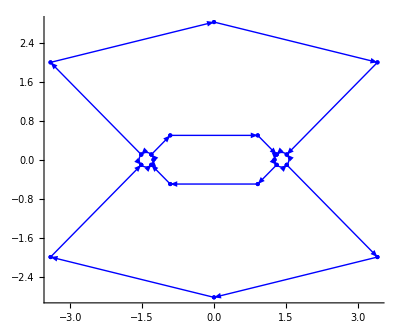

((1. | 0
0 | 1.) | -3.41421-2. ⅈ
(1. | 0
0 | 1.) | -3.41421+2. ⅈ
(1. | 0
0 | 1.) | -1.51995-0.105737 ⅈ
(1. | 0
0 | 1.) | -1.51995+0.105737 ⅈ
(1. | 0
0 | 1.) | -1.30848-0.105737 ⅈ
(1. | 0
0 | 1.) | -1.30848+0.105737 ⅈ
(1. | 0
0 | 1.) | -1.26468
(1. | 0
0 | 1.) | -0.914214-0.5 ⅈ
(1. | 0
0 | 1.) | -0.914214+0.5 ⅈ
(1. | 0
0 | 1.) | 0.-2.82843 ⅈ
(1. | 0
0 | 1.) | 0.+2.82843 ⅈ
(1. | 0
0 | 1.) | 0.914214-0.5 ⅈ
(1. | 0
0 | 1.) | 0.914214+0.5 ⅈ
(1. | 0
0 | 1.) | 1.26468
(1. | 0
0 | 1.) | 1.30848-0.105737 ⅈ
(1. | 0
0 | 1.) | 1.30848+0.105737 ⅈ
(1. | 0
0 | 1.) | 1.51995-0.105737 ⅈ
(1. | 0
0 | 1.) | 1.51995+0.105737 ⅈ
(1. | 0
0 | 1.) | 3.41421-2. ⅈ
(1. | 0
0 | 1.) | 3.41421+2. ⅈ)

43

42

136

138

136

138

43

42

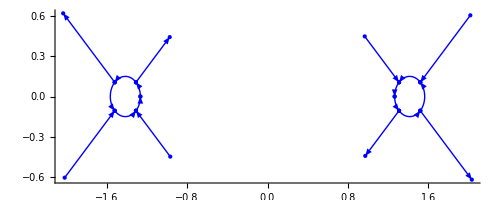

43

42

136

138

136

138

43

42

((1. | 0
0 | 1.) | -2.0326+0.61839 ⅈ
(1. | 0
0 | 1.) | -2.01768-0.603464 ⅈ
(1. | 0
0 | 1.) | -1.51995-0.105737 ⅈ
(1. | 0
0 | 1.) | -1.51995+0.105737 ⅈ
(1. | 0
0 | 1.) | -1.30848-0.105737 ⅈ
(1. | 0
0 | 1.) | -1.30848+0.105737 ⅈ
(1. | 0
0 | 1.) | -1.26468
(1. | 0
0 | 1.) | -0.972601+0.441613 ⅈ
(1. | 0
0 | 1.) | -0.967247-0.446967 ⅈ
(1. | 0
0 | 1.) | 0.967247+0.446967 ⅈ
(1. | 0
0 | 1.) | 0.972601-0.441613 ⅈ
(1. | 0
0 | 1.) | 1.26468
(1. | 0
0 | 1.) | 1.30848-0.105737 ⅈ
(1. | 0
0 | 1.) | 1.30848+0.105737 ⅈ
(1. | 0
0 | 1.) | 1.51995-0.105737 ⅈ
(1. | 0
0 | 1.) | 1.51995+0.105737 ⅈ
(1. | 0
0 | 1.) | 2.01768+0.603464 ⅈ
(1. | 0
0 | 1.) | 2.0326-0.61839 ⅈ)

```mathematica
(*On line segments*)
ΔPΔi[X_,v_][z_]:=Δ[v][z+I meps].Pmat[X,v][z].Δi[v][z+I meps];
ΔMΔi[X_,v_][z_]:=Δ[v][z+I meps].Mmat[X,v][z].Δi[v][z+I meps];
ΔLΔi[X_,v_][z_]:=Δ[v][z-I meps].Lmat[X,v][z].Δi[v][z-I meps];
ΔUΔi[X_,v_][z_]:=Δ[v][z-I meps].Umat[X,v][z].Δi[v][z-I meps];
(*On arcs*)
ΔDi[X_,v_][z_]:=Δ[v][z+I meps].DDi;
ΔMiDi[X_,v_][z_]:=Δ[v][z+I meps].Mmati[X,v][z].DDi;
ΔPiMiDi[X_,v_][z_]:=Δ[v][z].Pmati[X,v][z].Mmati[X,v][z].DDi;
ΔUPiMiDi[X_,v_][z_]:=Δ[v][z].Umat[X,v][z].Pmati[X,v][z].Mmati[X,v][z].DDi;

numptscirc=40;
smallradX[X_,v_]:=Min[Abs[X]^(-1/4),.4Abs[av[v]],.4Abs[bv[v]]];
acircpts[X_,v_]:={av[v]+smallradX[X,v],av[v]+smallradX[X,v]Exp[I Pi/4],av[v]+smallradX[X,v]Exp[I 3Pi/4], av[v]+smallradX[X,v]Exp[I 5Pi/4],av[v]+smallradX[X,v]Exp[-I Pi/4]};
bcircpts[X_,v_]:={bv[v]-smallradX[X,v],bv[v]+smallradX[X,v]Exp[I 3 Pi/4],bv[v]+smallradX[X,v]Exp[I Pi/4], bv[v]+smallradX[X,v]Exp[-I Pi/4],bv[v]+smallradX[X,v]Exp[I 5 Pi/4]};
JumpsLinesCirclesX[X_,v_]:={
Fun[ΔDi[X,v][#+I 100meps]&,Arc[av[v],smallradX[X,v],{0,Pi/4}],numptscirc],
Fun[ΔMiDi[X,v][#]&,Arc[av[v],smallradX[X,v],{Pi/4,3Pi/4}],numptscirc],
Fun[ΔPiMiDi[X,v][#]&,Arc[av[v],smallradX[X,v],{3Pi/4,5Pi/4}],numptscirc],
Fun[ΔUPiMiDi[X,v][#]&,Arc[av[v],smallradX[X,v],{-3Pi/4,-Pi/4}],numptscirc],
Fun[Δ[v][#-100meps I]&,Arc[av[v],smallradX[X,v],{-Pi/4,0}],numptscirc],

Fun[Δ[v][#-100meps I]&,Arc[bv[v],smallradX[X,v],{-Pi,-3Pi/4}],numptscirc],
Fun[ΔUPiMiDi[X,v][#]&,Arc[bv[v],smallradX[X,v],{-3Pi/4,-Pi/4}],numptscirc],
Fun[ΔPiMiDi[X,v][#]&,Arc[bv[v],smallradX[X,v],{-Pi/4,Pi/4}],numptscirc],
Fun[ΔMiDi[X,v][#]&,Arc[bv[v],smallradX[X,v],{Pi/4,3Pi/4}],numptscirc],
Fun[ΔDi[X,v][#+100meps I]&,Arc[bv[v],smallradX[X,v],{3Pi/4,Pi}],numptscirc],

Fun[ΔPΔi[X,v][#]&,Line[{acircpts[X,v][[3]],ptsUHPout[v][[2]]}],numpointsout],Fun[ΔPΔi[X,v][#]&,Line[{ptsUHPout[v][[2]],ptsUHPout[v][[3]]}],numpointsout],Fun[ΔPΔi[X,v][#]&,Line[{ptsUHPout[v][[3]],ptsUHPout[v][[4]]}],numpointsout],Fun[ΔPΔi[X,v][#]&,Line[{ptsUHPout[v][[4]],bcircpts[X,v][[3]]}],numpointsin],
Fun[ΔMΔi[X,v][#]&,Line[{acircpts[X,v][[2]],ptsUHPin[v][[2]]}],numpointsin],Fun[ΔMΔi[X,v][#]&,Line[{ptsUHPin[v][[2]],ptsUHPin[v][[3]]}],numpointsin],Fun[ΔMΔi[X,v][#]&,Line[{ptsUHPin[v][[3]],bcircpts[X,v][[2]]}],numpointsin],
Fun[ΔLΔi[X,v][#]&,Line[{bcircpts[X,v][[5]],ptsLHPin[v][[2]]}],numpointsin],Fun[ΔLΔi[X,v][#]&,Line[{ptsLHPin[v][[2]],ptsLHPin[v][[3]]}],numpointsin],Fun[ΔLΔi[X,v][#]&,Line[{ptsLHPin[v][[3]],acircpts[X,v][[5]]}],numpointsin],
Fun[ΔUΔi[X,v][#]&,Line[{bcircpts[X,v][[4]],ptsLHPout[v][[2]]}],numpointsout],Fun[ΔUΔi[X,v][#]&,Line[{ptsLHPout[v][[2]],ptsLHPout[v][[3]]}],numpointsout],Fun[ΔUΔi[X,v][#]&,Line[{ptsLHPout[v][[3]],ptsLHPout[v][[4]]}],numpointsout],Fun[ΔUΔi[X,v][#]&,Line[{ptsLHPout[v][[4]],acircpts[X,v][[4]]}],numpointsout]
};
(*Join[TruncatedLineContours[Pmat,ptsUHPout[v],numptsmax,numptsmin][X,v],TruncatedLineContours[Mmat,ptsUHPin[v],numptsmax,numptsmin][X,v],TruncatedLineContours[Lmat,ptsLHPin[v],numptsmax,numptsmin][X,v],TruncatedLineContours[Umat,ptsLHPout[v],numptsmax,numptsmin][X,v],{Fun[Dmat[X,v][#]&,Line[{av[v],bv[v]}],numpointsin]}];
*)
XtruncptsΔPΔi[X_,v_]:={acircpts[X,v][[3]],ptsUHPout[v][[2]],ptsUHPout[v][[3]],ptsUHPout[v][[4]],bcircpts[X,v][[3]]};
XtruncptsΔMΔi[X_,v_]:={acircpts[X,v][[2]],ptsUHPin[v][[2]],ptsUHPin[v][[3]],bcircpts[X,v][[2]]};
XtruncptsΔLΔi[X_,v_]:={bcircpts[X,v][[5]],ptsLHPin[v][[2]],ptsLHPin[v][[3]],acircpts[X,v][[5]]};
XtruncptsΔUΔi[X_,v_]:={bcircpts[X,v][[4]],ptsLHPout[v][[2]],ptsLHPout[v][[3]],ptsLHPout[v][[4]],acircpts[X,v][[4]]};
JumpsTruncLinesCirclesX[X_,v_]:=Join[
{Fun[ΔDi[X,v][#+I 100meps]&,Arc[av[v],smallradX[X,v],{0,Pi/4}],numptscirc]},
{Fun[ΔMiDi[X,v][#]&,Arc[av[v],smallradX[X,v],{Pi/4,3Pi/4}],numptscirc]},
{Fun[ΔPiMiDi[X,v][#]&,Arc[av[v],smallradX[X,v],{3Pi/4,5Pi/4}],numptscirc]},
{Fun[ΔUPiMiDi[X,v][#]&,Arc[av[v],smallradX[X,v],{-3Pi/4,-Pi/4}],numptscirc]},
{Fun[Δ[v][#-100meps I]&,Arc[av[v],smallradX[X,v],{-Pi/4,0}],numptscirc]},
{Fun[Δ[v][#-100meps I]&,Arc[bv[v],smallradX[X,v],{-Pi,-3Pi/4}],numptscirc]},
{Fun[ΔUPiMiDi[X,v][#]&,Arc[bv[v],smallradX[X,v],{-3Pi/4,-Pi/4}],numptscirc]},
{Fun[ΔPiMiDi[X,v][#]&,Arc[bv[v],smallradX[X,v],{-Pi/4,Pi/4}],numptscirc]},
{Fun[ΔMiDi[X,v][#]&,Arc[bv[v],smallradX[X,v],{Pi/4,3Pi/4}],numptscirc]},
{Fun[ΔDi[X,v][#+100meps I]&,Arc[bv[v],smallradX[X,v],{3Pi/4,Pi}],numptscirc]},
TruncatedLineContours[ΔPΔi,XtruncptsΔPΔi[X,v],numptsmax,numptsmin][X,v],TruncatedLineContours[ΔMΔi,XtruncptsΔMΔi[X,v],numptsmax,numptsmin][X,v],TruncatedLineContours[ΔLΔi,XtruncptsΔLΔi[X,v],numptsmax,numptsmin][X,v],TruncatedLineContours[ΔUΔi,XtruncptsΔUΔi[X,v],numptsmax,numptsmin][X,v]
];
xtest=2000;
vtest=0.;
JumpsLinesCirclesX[xtest,vtest]//DomainPlot
JumpsLinesCirclesX[xtest,vtest]//mRHWellPosed

JumpsTruncLinesCirclesX[xtest,vtest]//DomainPlot
JumpsTruncLinesCirclesX[xtest,vtest]//mRHWellPosed
RHLinesCirclesSolX[X_,v_]:=RHLinesCirclesSolX[X,v]=-((RHSolved[JumpsLinesCirclesX[X,v]])//DomainIntegrate)/(Pi);
nlsLinesCirclesX[X_,v_]:=Piecewise[{{RHLinesCirclesSolX[10^(-8),v][[1,2]]/Sqrt[10^(-8)],X==0},{RHLinesCirclesSolX[X,v][[1,2]]/Sqrt[X],True}}];

RHTruncLinesCirclesSolX[X_,v_]:=RHTruncLinesCirclesSolX[X,v]=-((RHSolved[JumpsTruncLinesCirclesX[X,v]])//DomainIntegrate)/(Pi);
nlsTruncLinesCirclesX[X_,v_]:=Piecewise[{{RHTruncLinesCirclesSolX[10^(-8),v][[1,2]]/Sqrt[10^(-8)],X==0},{RHTruncLinesCirclesSolX[X,v][[1,2]]/Sqrt[X],True}}];
```

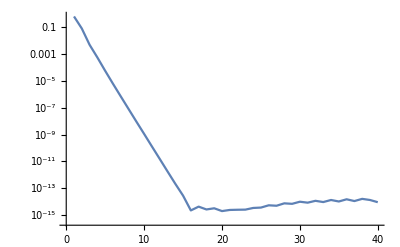
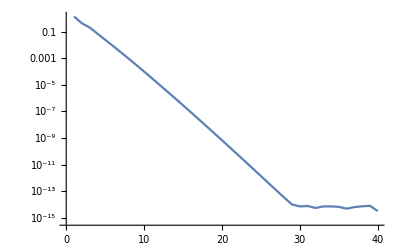
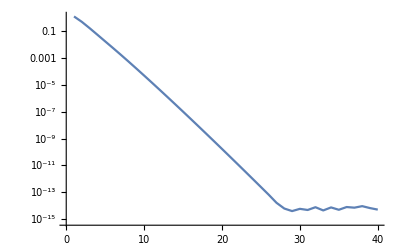
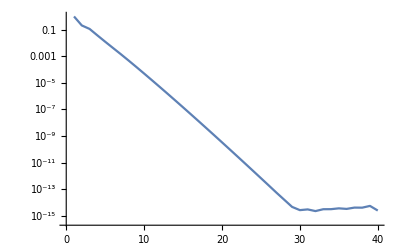
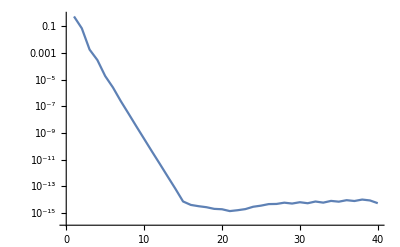
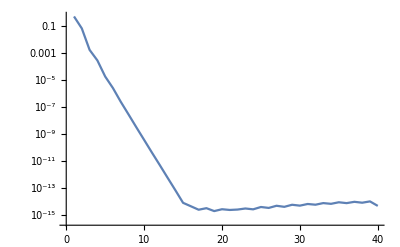
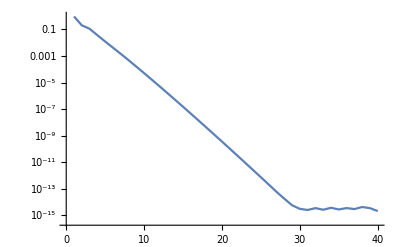
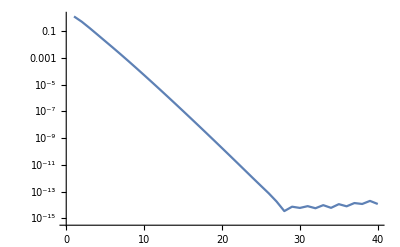

105

105

160

40

160

160

40

160

102

105

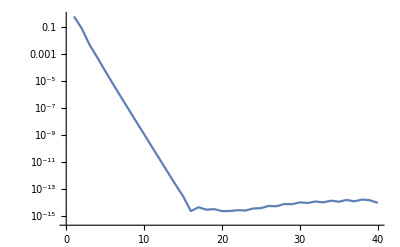
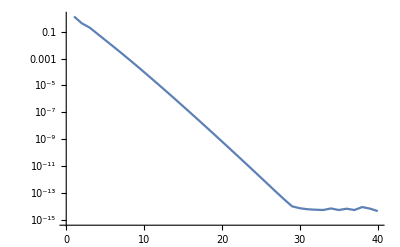
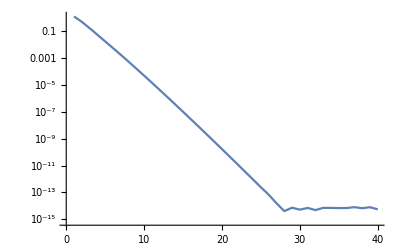
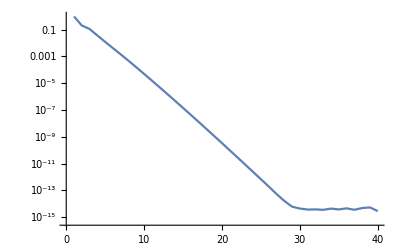
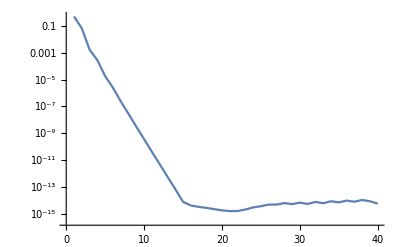
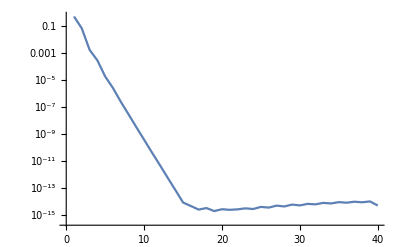
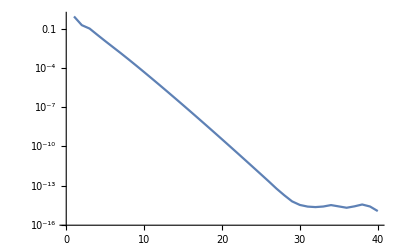
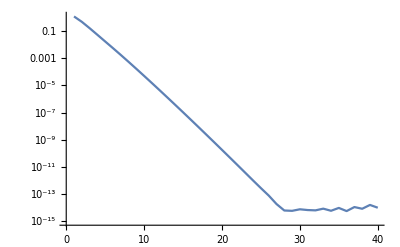

```mathematica
sol1=RHSolved[JumpsLinesCirclesX[Xtest,vtest]];
DCTPlot/@sol1
sol2=RHSolved[JumpsTruncLinesCirclesX[Xtest,vtest]];
DCTPlot/@sol2
```

## Asymptotic Formulae for large X, small 0≤ v<54^(-1/2)

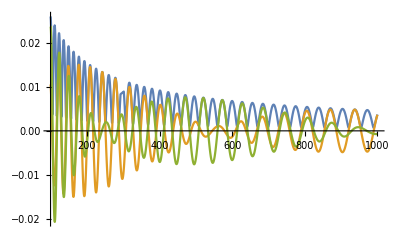

-0.00261934-0.00316774 ⅈ

```mathematica
p=Log[2]/(2Pi);
θ[v_][z_]:=z+v z^2+2/z;
θppa[v_]:=6v+2/av[v];
θppb[v_]:=6v+2/bv[v];
PsiAsympXv0[X_]:=(2^(5/4)/X^(3/4))*Sqrt[Log[2]/(2Pi)]Cos[4Sqrt[2]X^(1/2)-(Log[2]/(4Pi))Log[X]-9(Log[2])^2/(4Pi)-Pi/4+Arg[Gamma[I Log[2]/(2Pi)]]];
phi[X_,v_]:=-(p/2)*Log[X]-2p Log[bv[v]-av[v]]-Pi/4-2Pi*p^2+Arg[Gamma[I p]];
(*PsiAsympX[X,v X^(3/2)]=*)
vtest=0.05;
PsiAsympX[X_,v_]:=(Sqrt[2p]/(X^(3/4)))(Exp[-2I Sqrt[X]θ[v][av[v]]](-θppa[v])^(-I p)Exp[I phi[X,v]]/Sqrt[-θppa[v]]+Exp[-2I Sqrt[X]θ[v][bv[v]]](θppb[v])^(I p)Exp[-I phi[X,v]]/Sqrt[θppb[v]]);
Plot[{Abs[PsiAsympX[X,vtest]],Re[PsiAsympX[X,vtest]],Im[PsiAsympX[X,vtest]]},{X,100,1000},PlotRange->All]
(*PsiAsympX[200,vtest]*)
```

# Large-T deformation (Airy parametrices) - This is work in progress.

## R4-RHP for large T, small w: 0≤w<54^(1/3), X=wT^(2/3)

```mathematica
ptQ[z_,a_]:=(z==a);
θw[w_][z_]:=w*z+z^2+2/z;
θwp[w_][z_]:=w+2z-2/z^2;
adouble[w_]:=(1/2)(-w/6-Sqrt[w^2/36+2^(5/3)])//N;
bdouble[w_]:=(1/2)(-w/6+Sqrt[w^2/36+2^(5/3)])//N;
zsimplep[w_]:=(1/3)(-w+I Sqrt[54^(2/3)-w^2]);
zsimplem[w_]:=(1/3)(-w-I Sqrt[54^(2/3)-w^2]);
imppts[w_]:={adouble[w],bdouble[w],zsimplep[w],zsimplem[w]};
(*R and gfun has a branch cut consisting of two line segments [Subscript[z, 0],a] and [a,Subscript[z, o]^*].*)
(* IMPORTANT: they are both left continuous on the branch cut.*)
LineSqrt[z0_,a_][z_]:=Sqrt[(z-z0)/(z-a)](z-a);
R[w_][z_]:=LineSqrt[zsimplep[w],adouble[w]][z]*LineSqrt[adouble[w],zsimplem[w]][z]/(z-adouble[w]);
Rstd[w_][z_]:=Sqrt[z-zsimplep[w]]*Sqrt[z-zsimplem[w]];
RΣpL[w_][z_]:=-Rstd[w][z];
RΣmL[w_][z_]:=-Rstd[w][z];
RΣpR[w_][z_]:=Rstd[w][z];
RΣmR[w_][z_]:=Rstd[w][z];
RΓmR[w_][z_]:=Rstd[w][z];
RΓmL[w_][z_]:=Rstd[w][z];
RΓpL[w_][z_]:=Rstd[w][z];
RΓpR[w_][z_]:=Rstd[w][z];

gfunPrime[w_][z_]:=-θwp[w][z]+(2/z^2)(z-adouble[w])(z-bdouble[w])*R[w][z];
FwCore[w_][z_]:=-(R[w][z]/z)(z(2bdouble[w]+Re[zsimplep[w]]-z)+2adouble[w](bdouble[w]+z))+(2/Abs[zsimplep[w]])(bdouble[w]Abs[zsimplep[w]]^2+adouble[w](bdouble[w] Re[zsimplep[w]]+Abs[zsimplep[w]]^2))(Log[Abs[zsimplep[w]]^2+Abs[zsimplep[w]]R[w][z]- Re[zsimplep[w]] z]-Log[z])+(2 bdouble[w]  Re[zsimplep[w]]+2 adouble[w] (bdouble[w]+ Re[zsimplep[w]])+ Im[zsimplep[w]]^2) Log[- Re[zsimplep[w]]+R[w][z]+z];
FwCoreDepR[w_,R_][z_]:=-(R[w][z]/z)(z(2bdouble[w]+Re[zsimplep[w]]-z)+2adouble[w](bdouble[w]+z))+(2/Abs[zsimplep[w]])(bdouble[w]Abs[zsimplep[w]]^2+adouble[w](bdouble[w] Re[zsimplep[w]]+Abs[zsimplep[w]]^2))(Log[Abs[zsimplep[w]]^2+Abs[zsimplep[w]]R[w][z]- Re[zsimplep[w]] z]-Log[z])+(2 bdouble[w]  Re[zsimplep[w]]+2 adouble[w] (bdouble[w]+ Re[zsimplep[w]])+ Im[zsimplep[w]]^2) Log[- Re[zsimplep[w]]+R[w][z]+z];
Fw[w_][z_]:=FwCore[w][z+I meps]/;PossibleZeroQ[Re[z]];
Fw[w_][z_]:=0/;PossibleZeroQ[z-zsimplem[w]];
Fw[w_][z_]:=(FwCore[w][adouble[w]+I meps]//N//Chop)/;PossibleZeroQ[z-adouble[w]];
Fw[w_][z_]:=FwCore[w][z];
FwAtInfinity[w_]:=(w^2/6)+3/2^(1/3);
FwAtInfinityAlt[w_]:=-(w^2/6)-3/2^(1/3);
gfun[w_][z_]:=-θw[w][z]+Fw[w][z]-FwAtInfinity[w];
hfun[w_][z_]:=Fw[w][z]-FwAtInfinity[w];
hfunDepR[w_,R_][z_]:=FwCoreDepR[w,R][z]-FwAtInfinity[w];
convext=0.5;
cutpointp[w_]:=convext*zsimplep[w]+(1-convext)adouble[w];
cutpointm[w_]:=convext*zsimplem[w]+(1-convext)adouble[w];
(*κ[w_]:=gfun[w][cutpointp[w]-meps]+gfun[w][cutpointp[w]+meps]+2 θw[w][cutpointp[w]];*)
(* κ[w] is real valued for w on the branch cut Σ! *)
κ[w_]:=Re[hfun[w][cutpointp[w]-meps]+hfun[w][cutpointp[w]+meps]];
κR[w_]:=hfunDepR[w,RΣpL][cutpointp[w]-meps]+hfunDepR[w,RΣpR][cutpointp[w]+meps];
Series[gfun[1][z],{z,ComplexInfinity,2}]//N//Chop
κ[0]//Chop
κR[0]//Chop
```

-1.22482/z+0.817287/z^2+O[1/z]^3

-4.7622

-4.7622

## Jump matrices for general 0≤w<54^(1/3)

```mathematica
wcrit=54^(1/3);
JmatΓpL[w_,T_][z_]:={{1,0},{-Exp[2I T^(1/3)hfun[w][z]],1}};
JmatΓpLi[w_,T_][z_]:={{1,0},{Exp[2I T^(1/3)hfun[w][z]],1}};
JmatΓpR[w_,T_][z_]:={{1,(1/2)Exp[-2I T^(1/3)hfun[w][z]]},{0,1}};
JmatΓpRi[w_,T_][z_]:={{1,-(1/2)Exp[-2I T^(1/3)hfun[w][z]]},{0,1}};
JmatI[w_,T_][z_]=DiagonalMatrix[{2,1/2}];
JmatΓmR[w_,T_][z_]:={{1,0},{-(1/2)Exp[2I T^(1/3)hfun[w][z]],1}};
JmatΓmRi[w_,T_][z_]:={{1,0},{(1/2)Exp[2I T^(1/3)hfun[w][z]],1}};
JmatΓmL[w_,T_][z_]:={{1,Exp[-2I T^(1/3)hfun[w][z]]},{0,1}};
JmatΓmLi[w_,T_][z_]:={{1,-Exp[-2I T^(1/3)hfun[w][z]]},{0,1}};
JmatΣpL[w_,T_][z_]:={{1,-Exp[-2I T^(1/3)hfun[w][z-meps]]},{0,1}};
JmatΣpLi[w_,T_][z_]:={{1,Exp[-2I T^(1/3)hfun[w][z-meps]]},{0,1}};
JmatΣpR[w_,T_][z_]:={{1,-(1/2)Exp[-2I T^(1/3)hfun[w][z+meps]]},{0,1}};
JmatΣpRi[w_,T_][z_]:={{1,(1/2)Exp[-2I T^(1/3)hfun[w][z+meps]]},{0,1}};
JmatΣmR[w_,T_][z_]:={{1,0},{(1/2)Exp[2I T^(1/3)hfun[w][z+meps]],1}};
JmatΣmRi[w_,T_][z_]:={{1,0},{-(1/2)Exp[2I T^(1/3)hfun[w][z+meps]],1}};
JmatΣmL[w_,T_][z_]:={{1,0},{Exp[2I T^(1/3)hfun[w][z-meps]],1}};
JmatΣmLi[w_,T_][z_]:={{1,0},{-Exp[2I T^(1/3)hfun[w][z-meps]],1}};
JmatΣ[w_,T_][z_]:={{0,Exp[-I T^(1/3)Re[κ[w]]]},{-Exp[I T^(1/3)Re[κ[w]]],0}};


JmatNoPhaseΓpL[w_,T_][z_]:={{1,0},{-1,1}};
JmatNoPhaseΓpLi[w_,T_][z_]:={{1,0},{1,1}};
JmatNoPhaseΓpR[w_,T_][z_]:={{1,(1/2)},{0,1}};
JmatNoPhaseΓpRi[w_,T_][z_]:={{1,-(1/2)},{0,1}};
(*JmatI[w_,T_][z_]=DiagonalMatrix[{2,1/2}];*)
JmatNoPhaseΓmR[w_,T_][z_]:={{1,0},{-(1/2),1}};
JmatNoPhaseΓmRi[w_,T_][z_]:={{1,0},{(1/2),1}};
JmatNoPhaseΓmL[w_,T_][z_]:={{1,1},{0,1}};
JmatNoPhaseΓmLi[w_,T_][z_]:={{1,-1},{0,1}};
JmatNoPhaseΣpL[w_,T_][z_]:={{1,-1},{0,1}};
JmatNoPhaseΣpLi[w_,T_][z_]:={{1,1},{0,1}};
JmatNoPhaseΣpR[w_,T_][z_]:={{1,-(1/2)},{0,1}};
JmatNoPhaseΣpRi[w_,T_][z_]:={{1,(1/2)},{0,1}};
JmatNoPhaseΣmR[w_,T_][z_]:={{1,0},{(1/2),1}};
JmatNoPhaseΣmRi[w_,T_][z_]:={{1,0},{-(1/2),1}};
JmatNoPhaseΣmL[w_,T_][z_]:={{1,0},{1,1}};
JmatNoPhaseΣmLi[w_,T_][z_]:={{1,0},{-1,1}};
JmatNoPhaseΣ[w_,T_][z_]:={{0,1},{-1,0}};


JNoPhaseCircPlus[w_,T_][z_]:=DiagonalMatrix[{Exp[I T^(1/3)hfun[w][z]],Exp[-I T^(1/3)hfun[w][z]]}];
JNoPhaseCircPlusDepR[w_,T_,R_][z_]:=DiagonalMatrix[{Exp[I T^(1/3)hfunDepR[w,R][z]],Exp[-I T^(1/3)hfunDepR[w,R][z]]}];


JmatΓpLDepR[w_,T_][z_]:={{1,0},{-Exp[2I T^(1/3)hfunDepR[w,RΓpL][z]],1}};
JmatΓpLDepRi[w_,T_][z_]:={{1,0},{Exp[2I T^(1/3)hfunDepR[w,RΓpL][z]],1}};
JmatΓpRDepR[w_,T_][z_]:={{1,(1/2)Exp[-2I T^(1/3)hfunDepR[w,RΓpR][z]]},{0,1}};
JmatΓpRDepRi[w_,T_][z_]:={{1,-(1/2)Exp[-2I T^(1/3)hfunDepR[w,RΓpR][z]]},{0,1}};
JmatI[w_,T_][z_]=DiagonalMatrix[{2,1/2}];
JmatΓmRDepR[w_,T_][z_]:={{1,0},{-(1/2)Exp[2I T^(1/3)hfunDepR[w,RΓmR][z]],1}};
JmatΓmRDepRi[w_,T_][z_]:={{1,0},{(1/2)Exp[2I T^(1/3)hfunDepR[w,RΓmR][z]],1}};
JmatΓmLDepR[w_,T_][z_]:={{1,Exp[-2I T^(1/3)hfunDepR[w,RΓmL][z]]},{0,1}};
JmatΓmLDepRi[w_,T_][z_]:={{1,-Exp[-2I T^(1/3)hfunDepR[w,RΓmL][z]]},{0,1}};
JmatΣpLDepR[w_,T_][z_]:={{1,-Exp[-2I T^(1/3)hfunDepR[w,RΣpL][z]]},{0,1}};
JmatΣpLDepRi[w_,T_][z_]:={{1,Exp[-2I T^(1/3)hfunDepR[w,RΣpL][z]]},{0,1}};
JmatΣpRDepR[w_,T_][z_]:={{1,-(1/2)Exp[-2I T^(1/3)hfunDepR[w,RΣpR][z]]},{0,1}};
JmatΣpRDepRi[w_,T_][z_]:={{1,(1/2)Exp[-2I T^(1/3)hfunDepR[w,RΣpR][z]]},{0,1}};
JmatΣmRDepR[w_,T_][z_]:={{1,0},{(1/2)Exp[2I T^(1/3)hfunDepR[w,RΣmR][z]],1}};
JmatΣmRDepRi[w_,T_][z_]:={{1,0},{-(1/2)Exp[2I T^(1/3)hfunDepR[w,RΣmR][z]],1}};
JmatΣmLDepR[w_,T_][z_]:={{1,0},{Exp[2I T^(1/3)hfunDepR[w,RΣmL][z]],1}};
JmatΣmLDepRi[w_,T_][z_]:={{1,0},{-Exp[2I T^(1/3)hfunDepR[w,RΣmL][z]],1}};
JmatΣDepR[w_,T_][z_]:={{0,Exp[-I T^(1/3)Re[κR[w]]]},{-Exp[I T^(1/3)Re[κR[w]]],0}};

pΣpL[w_]:=Piecewise[{{adouble[w]+(-1+I)0.5*Im[zsimplep[w]],w≤ 3},{adouble[w]+(-3+I)0.5*Im[zsimplep[w]],w>3}}];
pΣmL[w_]:=Piecewise[{{adouble[w]+(-1-I)0.5*Im[zsimplep[w]],w≤ 3},{adouble[w]+(-3-I)0.5*Im[zsimplep[w]],w> 3}}];

pΣpR[w_]:=Piecewise[{{adouble[w]+Exp[I Arg[zsimplep[w]-adouble[w]]/3]0.5*Im[zsimplep[w]]/Sin[Arg[zsimplep[w]-adouble[w]]/2],w≥ 0.5},{Re[zsimplep[w]]-w+(I/3)*Im[zsimplep[w]],w≤ 0.5}}];
pΣmR[w_]:=Piecewise[{{adouble[w]+Exp[-I Arg[zsimplep[w]-adouble[w]]/3]0.5*Im[zsimplep[w]]/Sin[Arg[zsimplep[w]-adouble[w]]/2],w≥ 0.5},{Re[zsimplep[w]]-w-(I/3)*Im[zsimplep[w]],w≤ 0.5}}];

(* The points should be edited for w=0. IN PROGRESS. *)
ptsΣpLw0:={adouble[0],adouble[0]+(-1+I)0.5Im[zsimplep[0]],zsimplep[0]};
ptsΣpRw0:={adouble[0],0.1adouble[0]+0.5zsimplep[0],zsimplep[0]};
(*ptsΓpL[w_]:={zsimplep[w],((wcrit-w)/wcrit)bdouble[w]+(w/wcrit)Re[zsimplep[w]]+I 1.5Im[zsimplep[w]],bdouble[w]+(1+I)Im[zsimplep[w]]1.5,bdouble[w]};*)
ptsΓpRw0:={zsimplep[0],zsimplep[0]0.5,bdouble[0]};
ptsΓpLw0:={zsimplep[0],1.5(bdouble[0]+zsimplep[0]),bdouble[0]};
ptsΣmLw0:={adouble[0],adouble[0]+(-1-I)0.5Im[zsimplep[0]],zsimplem[0]}//Reverse;
ptsΣmRw0:={adouble[0],0.1adouble[0]+0.5zsimplem[0],zsimplem[0]}//Reverse;
ptsΓmRw0:={zsimplem[0],zsimplem[0]0.5,bdouble[0]}//Reverse;
ptsΓmLw0:={zsimplem[0],1.5(bdouble[0]+zsimplem[0]),bdouble[0]}//Reverse;
(*****)
ptsΣpL[w_]:={adouble[w],pΣpL[w],zsimplep[w]};
ptsΣpR[w_]:={adouble[w],pΣpR[w],zsimplep[w]};
(*ptsΓpL[w_]:={zsimplep[w],((wcrit-w)/wcrit)bdouble[w]+(w/wcrit)Re[zsimplep[w]]+I 1.5Im[zsimplep[w]],bdouble[w]+(1+I)Im[zsimplep[w]]1.5,bdouble[w]};*)
ptsΓpL[w_]:={zsimplep[w],zsimplep[w]+Exp[I(Pi/2-((wcrit-w)/wcrit)Pi/4)]Im[zsimplep[0]],bdouble[w]+(1+I)Im[zsimplep[0]]1.5,bdouble[w]};
ptsΓpR[w_]:={zsimplep[w],bdouble[w]+(1/Sqrt[2])(-1+I)Im[zsimplep[w]],bdouble[w]}(*/;w≤3*);
(*ptsΓpR[w_]:={zsimplep[w],bdouble[w]};*)
ptsΣmL[w_]:={adouble[w],pΣmL[w],zsimplem[w]}//Reverse;
ptsΣmR[w_]:={adouble[w],pΣmR[w],zsimplem[w]}//Reverse;
(*ptsΓmL[w_]:={zsimplem[w],((wcrit-w)/wcrit)bdouble[w]+(w/wcrit)Re[zsimplep[w]]-I 1.5Im[zsimplep[w]],bdouble[w]+(1-I)Im[zsimplep[w]]1.5,bdouble[w]}//Reverse;*)
ptsΓmL[w_]:={zsimplem[w],zsimplem[w]+Exp[-I(Pi/2-((wcrit-w)/wcrit)Pi/4)]Im[zsimplep[0]],bdouble[w]+(1-I)Im[zsimplep[0]]1.5,bdouble[w]}//Reverse;
ptsΓmR[w_]:=Reverse[{zsimplem[w],bdouble[w]+(1/Sqrt[2])(-1-I)Im[zsimplep[w]],bdouble[w]}](*/;w≤3*);
(*ptsΓmR[w_]:=Reverse[{zsimplem[w],bdouble[w]}];*)
```

#### Parameters and jumps for the little circles used in order to stay away from half-integer behavior at the Airy-type points

```mathematica
Series[hfun[1][z]-hfun[1][zsimplep[1]],{z,zsimplep[1],2}]//N//Chop
```

(2.61273+1.48778 ⅈ) (z+(0.333333-1.21503 ⅈ))^(3/2)+O[z+(0.333333-1.21503 ⅈ)]^(5/2)

```mathematica
Series[hfun[0.][z]-hfun[0.][zsimplep[0.]],{z,zsimplep[0.],2}]//N//Chop
```

(2.24492+2.24492 ⅈ) (z-(0.+1.25992 ⅈ))^(3/2)+O[z-(0.+1.25992 ⅈ)]^(5/2)

```mathematica
(*smallrad[T_]:=T^(-2/9);*)
0.25^(-2/9)
smallrad[w_,T_]:=Piecewise[{{Min[{T^(-2/9),Im[zsimplep[w]]/2.0}],T≥ 10},{Min[{T^(-2/9)/5.,Im[zsimplep[w]]/2.0}],T<10}}];
Print["This should be big for T>>1."]
JmatΣpL[1,10^6][zsimplep[1]+I]//N
Print["But, these should be O(1) for T>>1."]
JmatΣpL[1,10^6][zsimplep[1]+smallrad[2,10^6]I]//N
Manipulate[JNoPhaseCircPlus[1,10^6][zsimplep[1]+smallrad[2,10^6]Exp[I theta]]//N,{theta,0,2Pi}]
```

1.36079

This should be big for T>>1.

{{1.,3.03045×10^36-3.38451×10^36 ⅈ},{0.,1.}}

But, these should be O(1) for T>>1.

{{1.,-4.57379-0.496229 ⅈ},{0.,1.}}

```mathematica
(*Little circle points in the UHP. Ordered clockwise, starting from the intersection of the circle with the contour Σ (the branch cut).*)
(*ArgPlusΣ[w_,T_]:=Arg[smallrad[w,T]*(adouble[w]-zsimplep[w])];
ArgMinusΣ[w_,T_]:=Arg[smallrad[w,T]*(adouble[w]-zsimplem[w])];*)
ArgPlusΣ[w_,T_]:=Arg[(adouble[w]-zsimplep[w])];
ArgMinusΣ[w_,T_]:=Arg[(adouble[w]-zsimplem[w])];
(*This is ordered clockwise*)
CirclePlusPts[w_,T_]:={zsimplep[w]+smallrad[w,T]Exp[I ArgPlusΣ[w,T]],zsimplep[w]+smallrad[w,T]Exp[I (ArgPlusΣ[w,T]-Pi/4)],zsimplep[w]+smallrad[w,T]Exp[I (ArgPlusΣ[w,T]+Pi)],zsimplep[w]+smallrad[w,T]Exp[I (ArgPlusΣ[w,T]+Pi/4)],zsimplep[w]+smallrad[w,T]Exp[I (ArgPlusΣ[w,T])]};
(*This is ordered clockwise*)
CircleMinusPts[w_,T_]:={zsimplem[w]+smallrad[w,T]Exp[I ArgMinusΣ[w,T]],zsimplem[w]+smallrad[w,T]Exp[I (ArgMinusΣ[w,T]-Pi/4)],zsimplem[w]+smallrad[w,T]Exp[I (ArgMinusΣ[w,T]+Pi)],zsimplem[w]+smallrad[w,T]Exp[I (ArgMinusΣ[w,T]+Pi/4)],zsimplem[w]+smallrad[w,T]Exp[I (ArgMinusΣ[w,T])]}; 

CirclePlusPtsw0[T_]:={zsimplep[0]+smallrad[0,T]Exp[I ArgPlusΣ[0,T]],zsimplep[0]+smallrad[0,T]Exp[I (ArgPlusΣ[0,T]-Pi/4)],zsimplep[0]+smallrad[0,T]Exp[I (ArgPlusΣ[0,T]+Pi)],zsimplep[0]+smallrad[0,T]Exp[I (ArgPlusΣ[0,T]+Pi/4)],zsimplep[0]+smallrad[0,T]Exp[I (ArgPlusΣ[0,T])]};
(*This is ordered clockwise*)
CircleMinusPtsw0[T_]:={zsimplem[0]+smallrad[0,T]Exp[I ArgMinusΣ[0,T]],zsimplem[0]+smallrad[0,T]Exp[I (ArgMinusΣ[0,T]-Pi/4)],zsimplem[0]+smallrad[0,T]Exp[I (ArgMinusΣ[0,T]+Pi)],zsimplem[0]+smallrad[0,T]Exp[I (ArgMinusΣ[0,T]+Pi/4)],zsimplem[0]+smallrad[0,T]Exp[I (ArgMinusΣ[0,T])]};

(*JmatΣpL[w_,T_][z_]:={{1,-Exp[-2I T^(1/3)hfun[w][z-meps]]},{0,1}};*)
H1[w_,T_][z_]:=JmatΣpL[w,T][z];
H1leftDepR[w_,T_][z_]:={{1,-Exp[-2I T^(1/3)hfunDepR[w,RΣpL][z]]},{0,1}};
H1leftDepRi[w_,T_][z_]:={{1,Exp[-2I T^(1/3)hfunDepR[w,RΣpL][z]]},{0,1}};
H1rightDepR[w_,T_][z_]:={{1,-Exp[-2I T^(1/3)hfunDepR[w,RΣpR][z]]},{0,1}};
(*Jplus[w_,T_][z_]:=H1leftDepRi[w,T][z].H1rightDepR[w,T][z];*)
H1H2i[w_,T_][z_]:=JmatΣpL[w,T][z].JmatΓpLi[w,T][z];
H1H2iH3iH4[w_,T_][z_]:=JmatΣpL[w,T][z+100meps].JmatΓpLi[w,T][z+100meps].JmatΓpRi[w,T][z+100meps].JmatΣpR[w,T][z+100meps];

(*jumpdummy[z_]:=IdentityMatrix[2];*)
numpointsin=80;
numpointsout=80;
```

Deformations with little circles at w=0

```mathematica
JumpsLittleCirclesw0[T_]:={
Fun[JNoPhaseCircPlusDepR[0,T,RΣpL][# ]&,Arc[zsimplep[0],smallrad[0,T],{ArgPlusΣ[0,T],ArgPlusΣ[0,T]-Pi/4}],numpointsin],
Fun[JNoPhaseCircPlusDepR[0,T,RΣpL][#-100I meps]&,Arc[zsimplep[0],smallrad[0,T],{ArgPlusΣ[0,T]-Pi/4,-Pi}],numpointsin],
Fun[JNoPhaseCircPlusDepR[0,T,RΣpR][#+100I meps]&,Arc[zsimplep[0],smallrad[0,T],{-Pi,ArgPlusΣ[0,T]-Pi}],numpointsin],
Fun[JNoPhaseCircPlusDepR[0,T,RΣpR][#]&,Arc[zsimplep[0],smallrad[0,T],{ArgPlusΣ[0,T]+Pi,ArgPlusΣ[0,T]+Pi/4}],numpointsin],
Fun[JNoPhaseCircPlusDepR[0,T,RΣpR][#]&,Arc[zsimplep[0],smallrad[0,T],{ArgPlusΣ[0,T]+Pi/4,ArgPlusΣ[0,T]}],numpointsin],
Fun[JNoPhaseCircPlusDepR[0,T,RΣmR][#]&,Arc[zsimplem[0],smallrad[0,T],{ArgMinusΣ[0,T],ArgMinusΣ[0,T]-Pi/4}],numpointsin],
Fun[JNoPhaseCircPlusDepR[0,T,RΣmR][#]&,Arc[zsimplem[0],smallrad[0,T],{ArgMinusΣ[0,T]-Pi/4,ArgMinusΣ[0,T]-Pi}],numpointsin],
Fun[JNoPhaseCircPlusDepR[0,T,RΣmR][#-I 100meps]&,Arc[zsimplem[0],smallrad[0,T],{ArgMinusΣ[0,T]-Pi,-Pi}],numpointsin],
Fun[JNoPhaseCircPlusDepR[0,T,RΣmL][#+I 100meps]&,Arc[zsimplem[0],smallrad[0,T],{Pi,ArgMinusΣ[0,T]+Pi/4}],numpointsin],
Fun[JNoPhaseCircPlusDepR[0,T,RΣmL][#]&,Arc[zsimplem[0],smallrad[0,T],{ArgMinusΣ[0,T]+Pi/4,ArgMinusΣ[0,T]}],numpointsin],
Fun[JmatNoPhaseΣpL[0,T][#]&,Line[{CirclePlusPtsw0[T][[2]],zsimplep[0]}],numpointsin],
Fun[JmatNoPhaseΓpL[0,T][#]&,Line[{zsimplep[0],CirclePlusPtsw0[T][[3]]}],numpointsin],
(*Fun[JmatNoPhaseΓpR[0,T][#]&,Line[{zsimplep[0],CirclePlusPtsw0[0,T][[4]]}],numpointsin],*)
Fun[JmatNoPhaseΓpRi[0,T][#].JmatNoPhaseΣpR[0,T][#]&,Line[{CirclePlusPtsw0[T][[4]],zsimplep[0]}],numpointsin],
Fun[JmatNoPhaseΣ[0,T][#]&,Line[{CirclePlusPtsw0[T][[1]],zsimplep[0]}],numpointsin],
Fun[JmatNoPhaseΣ[0,T][#]&,Line[{zsimplem[0],CircleMinusPtsw0[T][[1]]}],numpointsin],
Fun[JmatNoPhaseΓmRi[0,T][#].JmatNoPhaseΣmR[0,T][#]&,Line[{zsimplem[0],CircleMinusPtsw0[T][[2]]}],numpointsin],
Fun[JmatNoPhaseΓmL[0,T][#]&,Line[{CircleMinusPtsw0[T][[3]],zsimplem[0]}],numpointsin],
Fun[JmatNoPhaseΣmL[0,T][#]&,Line[{zsimplem[0],CircleMinusPtsw0[T][[4]]}],numpointsin],
Fun[JmatΣ[0,T][#]&,Line[{CircleMinusPtsw0[T][[1]],adouble[0]}],numpointsout],
Fun[JmatΣ[0,T][#]&,Line[{adouble[0],CirclePlusPtsw0[T][[1]]}],numpointsout],
Fun[JmatΣpLDepR[0,T][#]&,Line[{ptsΣpL[0][[1]],ptsΣpL[0][[2]]}],numpointsout],
Fun[JmatΣpLDepR[0,T][#]&,Line[{ptsΣpL[0][[2]],CirclePlusPtsw0[T][[2]]}],numpointsout],
Fun[JmatΓpLDepR[0,T][#]&,Line[{CirclePlusPtsw0[T][[3]],ptsΓpL[0][[2]]}],numpointsout],
Fun[JmatΓpLDepR[0,T][#]&,Line[{ptsΓpL[0][[2]],ptsΓpL[0][[3]]}],numpointsout],
Fun[JmatΓpLDepR[0,T][#]&,Line[{ptsΓpL[0][[3]],ptsΓpL[0][[4]]}],numpointsout],
Fun[JmatΓmLDepR[0,T][#]&,Line[{ptsΓmL[0][[1]],ptsΓmL[0][[2]]}],numpointsout],
Fun[JmatΓmLDepR[0,T][#]&,Line[{ptsΓmL[0][[2]],ptsΓmL[0][[3]]}],numpointsout],
Fun[JmatΓmLDepR[0,T][#]&,Line[{ptsΓmL[0][[3]],CircleMinusPtsw0[T][[3]]}],numpointsout],
Fun[JmatΣpRDepR[0,T][#]&,Line[{ptsΣpR[0][[1]],ptsΣpR[0][[2]]}],numpointsout],
Fun[JmatΣpRDepR[0,T][#]&,Line[{ptsΣpR[0][[2]],CirclePlusPtsw0[T][[4]]}],numpointsout],
Fun[JmatΓpRDepR[0,T][#]&,Line[{CirclePlusPtsw0[T][[4]],ptsΓpR[0][[3]]}],numpointsout],
Fun[JmatΓmRDepR[0,T][#]&,Line[{ptsΓmR[0][[1]],CircleMinusPtsw0[T][[2]]}],numpointsout],
Fun[JmatΣmRDepR[0,T][#]&,Line[{CircleMinusPtsw0[T][[2]],ptsΣmR[0][[2]]}],numpointsout],
Fun[JmatΣmRDepR[0,T][#]&,Line[{ptsΣmR[0][[2]],ptsΣmR[0][[3]]}],numpointsout],
Fun[JmatΣmLDepR[0,T][#]&,Line[{CircleMinusPtsw0[T][[4]],ptsΣmL[0][[2]]}],numpointsout],
Fun[JmatΣmLDepR[0,T][#]&,Line[{ptsΣmL[0][[2]],ptsΣmL[0][[3]]}],numpointsout],
Fun[JmatI[0,T][#]&,Line[{adouble[0],bdouble[0]}],numpointsout]};
```

Deformations with little circles for w>0

```mathematica
Clear[JumpsLittleCircles];
```

```mathematica
JumpsLittleCircles[w_,T_]:={
Fun[JNoPhaseCircPlusDepR[w,T,RΣpL][# ]&,Arc[zsimplep[w],smallrad[w,T],{ArgPlusΣ[w,T],ArgPlusΣ[w,T]-Pi/4}],numpointsin],
Fun[JNoPhaseCircPlusDepR[w,T,RΣpL][#-1000I meps]&,Arc[zsimplep[w],smallrad[w,T],{ArgPlusΣ[w,T]-Pi/4,-Pi}],numpointsin],
Fun[JNoPhaseCircPlusDepR[w,T,RΣpR][#+1000I meps]&,Arc[zsimplep[w],smallrad[w,T],{-Pi,ArgPlusΣ[w,T]-Pi}],numpointsin],
Fun[JNoPhaseCircPlusDepR[w,T,RΣpR][#]&,Arc[zsimplep[w],smallrad[w,T],{ArgPlusΣ[w,T]+Pi,ArgPlusΣ[w,T]+Pi/4}],numpointsin],
Fun[JNoPhaseCircPlusDepR[w,T,RΣpR][#]&,Arc[zsimplep[w],smallrad[w,T],{ArgPlusΣ[w,T]+Pi/4,ArgPlusΣ[w,T]}],numpointsin],
Fun[JNoPhaseCircPlusDepR[w,T,RΣmR][#]&,Arc[zsimplem[w],smallrad[w,T],{ArgMinusΣ[w,T],ArgMinusΣ[w,T]-Pi/4}],numpointsin],
Fun[JNoPhaseCircPlusDepR[w,T,RΣmR][#]&,Arc[zsimplem[w],smallrad[w,T],{ArgMinusΣ[w,T]-Pi/4,ArgMinusΣ[w,T]-Pi}],numpointsin],
Fun[JNoPhaseCircPlusDepR[w,T,RΣmR][#-I 1000meps]&,Arc[zsimplem[w],smallrad[w,T],{ArgMinusΣ[w,T]-Pi,-Pi}],numpointsin],
Fun[JNoPhaseCircPlusDepR[w,T,RΣmL][#+I 1000meps]&,Arc[zsimplem[w],smallrad[w,T],{Pi,ArgMinusΣ[w,T]+Pi/4}],numpointsin],
Fun[JNoPhaseCircPlusDepR[w,T,RΣmL][#]&,Arc[zsimplem[w],smallrad[w,T],{ArgMinusΣ[w,T]+Pi/4,ArgMinusΣ[w,T]}],numpointsin],
Fun[JmatNoPhaseΣpL[w,T][#]&,Line[{CirclePlusPts[w,T][[2]],zsimplep[w]}],numpointsin],
Fun[JmatNoPhaseΓpL[w,T][#]&,Line[{zsimplep[w],CirclePlusPts[w,T][[3]]}],numpointsin],
(*Fun[JmatNoPhaseΓpR[w,T][#]&,Line[{zsimplep[w],CirclePlusPts[w,w,T][[4]]}],numpointsin],*)
Fun[JmatNoPhaseΓpRi[w,T][#].JmatNoPhaseΣpR[w,T][#]&,Line[{CirclePlusPts[w,T][[4]],zsimplep[w]}],numpointsin],
Fun[JmatNoPhaseΣ[w,T][#]&,Line[{CirclePlusPts[w,T][[1]],zsimplep[w]}],numpointsin],
Fun[JmatNoPhaseΣ[w,T][#]&,Line[{zsimplem[w],CircleMinusPts[w,T][[1]]}],numpointsin],
Fun[JmatNoPhaseΓmRi[w,T][#].JmatNoPhaseΣmR[w,T][#]&,Line[{zsimplem[w],CircleMinusPts[w,T][[2]]}],numpointsin],
Fun[JmatNoPhaseΓmL[w,T][#]&,Line[{CircleMinusPts[w,T][[3]],zsimplem[w]}],numpointsin],
Fun[JmatNoPhaseΣmL[w,T][#]&,Line[{zsimplem[w],CircleMinusPts[w,T][[4]]}],numpointsin],
Fun[JmatΣ[w,T][#]&,Line[{CircleMinusPts[w,T][[1]],adouble[w]}],numpointsout],
Fun[JmatΣ[w,T][#]&,Line[{adouble[w],CirclePlusPts[w,T][[1]]}],numpointsout],
Fun[JmatΣpLDepR[w,T][#]&,Line[{ptsΣpL[w][[1]],ptsΣpL[w][[2]]}],numpointsout],
Fun[JmatΣpLDepR[w,T][#]&,Line[{ptsΣpL[w][[2]],CirclePlusPts[w,T][[2]]}],numpointsout],
Fun[JmatΓpLDepR[w,T][#]&,Line[{CirclePlusPts[w,T][[3]],ptsΓpL[w][[2]]}],numpointsout],
Fun[JmatΓpLDepR[w,T][#]&,Line[{ptsΓpL[w][[2]],ptsΓpL[w][[3]]}],numpointsout],
Fun[JmatΓpLDepR[w,T][#]&,Line[{ptsΓpL[w][[3]],ptsΓpL[w][[4]]}],numpointsout],
Fun[JmatΓmLDepR[w,T][#]&,Line[{ptsΓmL[w][[1]],ptsΓmL[w][[2]]}],numpointsout],
Fun[JmatΓmLDepR[w,T][#]&,Line[{ptsΓmL[w][[2]],ptsΓmL[w][[3]]}],numpointsout],
Fun[JmatΓmLDepR[w,T][#]&,Line[{ptsΓmL[w][[3]],CircleMinusPts[w,T][[3]]}],numpointsout],
Fun[JmatΣpRDepR[w,T][#]&,Line[{ptsΣpR[w][[1]],ptsΣpR[w][[2]]}],numpointsout],
Fun[JmatΣpRDepR[w,T][#]&,Line[{ptsΣpR[w][[2]],CirclePlusPts[w,T][[4]]}],numpointsout],
Fun[JmatΓpRDepR[w,T][#]&,Line[{CirclePlusPts[w,T][[4]],ptsΓpR[w][[3]]}],numpointsout+10],
Fun[JmatΓmRDepR[w,T][#]&,Line[{ptsΓmR[w][[1]],CircleMinusPts[w,T][[2]]}],numpointsout+10],
Fun[JmatΣmRDepR[w,T][#]&,Line[{CircleMinusPts[w,T][[2]],ptsΣmR[w][[2]]}],numpointsout],
Fun[JmatΣmRDepR[w,T][#]&,Line[{ptsΣmR[w][[2]],ptsΣmR[w][[3]]}],numpointsout],
Fun[JmatΣmLDepR[w,T][#]&,Line[{CircleMinusPts[w,T][[4]],ptsΣmL[w][[2]]}],numpointsout],
Fun[JmatΣmLDepR[w,T][#]&,Line[{ptsΣmL[w][[2]],ptsΣmL[w][[3]]}],numpointsout],
Fun[JmatI[w,T][#]&,Line[{adouble[w],bdouble[w]}],numpointsout]}(*/;w≤3*);

(*Contour Truncation*)
ptsWithCirclesΣpL[w_,T_]:={ptsΣpL[w][[1]],ptsΣpL[w][[2]],CirclePlusPts[w,T][[2]]};
ptsWithCirclesΓpL[w_,T_]:={CirclePlusPts[w,T][[3]],ptsΓpL[w][[2]],ptsΓpL[w][[3]],ptsΓpL[w][[4]]};
ptsWithCirclesΓmL[w_,T_]:={ptsΓmL[w][[1]],ptsΓmL[w][[2]],ptsΓmL[w][[3]],CircleMinusPts[w,T][[3]]};
ptsWithCirclesΣpR[w_,T_]:={ptsΣpR[w][[1]],ptsΣpR[w][[2]],CirclePlusPts[w,T][[4]]};
ptsWithCirclesΓpR[w_,T_]:={CirclePlusPts[w,T][[4]],ptsΓpR[w][[3]]};
ptsWithCirclesΓmR[w_,T_]:={ptsΓmR[w][[1]],CircleMinusPts[w,T][[2]]};
ptsWithCirclesΣmR[w_,T_]:={CircleMinusPts[w,T][[2]],ptsΣmR[w][[2]],ptsΣmR[w][[3]]};
ptsWithCirclesΣmL[w_,T_]:={CircleMinusPts[w,T][[4]],ptsΣmL[w][[2]],ptsΣmL[w][[3]]};

JumpsTruncLittleCircles[w_,T_]:=Join[
{Fun[JNoPhaseCircPlusDepR[w,T,RΣpL][# ]&,Arc[zsimplep[w],smallrad[w,T],{ArgPlusΣ[w,T],ArgPlusΣ[w,T]-Pi/4}],numpointsin]},
{Fun[JNoPhaseCircPlusDepR[w,T,RΣpL][#-100I meps]&,Arc[zsimplep[w],smallrad[w,T],{ArgPlusΣ[w,T]-Pi/4,-Pi}],numpointsin]},
{Fun[JNoPhaseCircPlusDepR[w,T,RΣpR][#+100I meps]&,Arc[zsimplep[w],smallrad[w,T],{-Pi,ArgPlusΣ[w,T]-Pi}],numpointsin]},
{Fun[JNoPhaseCircPlusDepR[w,T,RΣpR][#]&,Arc[zsimplep[w],smallrad[w,T],{ArgPlusΣ[w,T]+Pi,ArgPlusΣ[w,T]+Pi/4}],numpointsin]},
{Fun[JNoPhaseCircPlusDepR[w,T,RΣpR][#]&,Arc[zsimplep[w],smallrad[w,T],{ArgPlusΣ[w,T]+Pi/4,ArgPlusΣ[w,T]}],numpointsin]},
{Fun[JNoPhaseCircPlusDepR[w,T,RΣmR][#]&,Arc[zsimplem[w],smallrad[w,T],{ArgMinusΣ[w,T],ArgMinusΣ[w,T]-Pi/4}],numpointsin]},
{Fun[JNoPhaseCircPlusDepR[w,T,RΣmR][#]&,Arc[zsimplem[w],smallrad[w,T],{ArgMinusΣ[w,T]-Pi/4,ArgMinusΣ[w,T]-Pi}],numpointsin]},
{Fun[JNoPhaseCircPlusDepR[w,T,RΣmR][#-I 100meps]&,Arc[zsimplem[w],smallrad[w,T],{ArgMinusΣ[w,T]-Pi,-Pi}],numpointsin]},
{Fun[JNoPhaseCircPlusDepR[w,T,RΣmL][#+I 100meps]&,Arc[zsimplem[w],smallrad[w,T],{Pi,ArgMinusΣ[w,T]+Pi/4}],numpointsin]},
{Fun[JNoPhaseCircPlusDepR[w,T,RΣmL][#]&,Arc[zsimplem[w],smallrad[w,T],{ArgMinusΣ[w,T]+Pi/4,ArgMinusΣ[w,T]}],numpointsin]},
{Fun[JmatNoPhaseΣpL[w,T][#]&,Line[{CirclePlusPts[w,T][[2]],zsimplep[w]}],numpointsin]},
{Fun[JmatNoPhaseΓpL[w,T][#]&,Line[{zsimplep[w],CirclePlusPts[w,T][[3]]}],numpointsin]},
{Fun[JmatΣ[w,T][#]&,Line[{CircleMinusPts[w,T][[1]],adouble[w]}],numpointsout]},
{Fun[JmatΣ[w,T][#]&,Line[{adouble[w],CirclePlusPts[w,T][[1]]}],numpointsout]},
(*Fun[JmatNoPhaseΓpR[w,T][#]&,Line[{zsimplep[w],CirclePlusPts[w,w,T][[4]]}],numpointsin],*)
{Fun[JmatNoPhaseΓpRi[w,T][#].JmatNoPhaseΣpR[w,T][#]&,Line[{CirclePlusPts[w,T][[4]],zsimplep[w]}],numpointsin]},
{Fun[JmatNoPhaseΣ[w,T][#]&,Line[{CirclePlusPts[w,T][[1]],zsimplep[w]}],numpointsin]},
{Fun[JmatNoPhaseΣ[w,T][#]&,Line[{zsimplem[w],CircleMinusPts[w,T][[1]]}],numpointsin]},
{Fun[JmatNoPhaseΓmRi[w,T][#].JmatNoPhaseΣmR[w,T][#]&,Line[{zsimplem[w],CircleMinusPts[w,T][[2]]}],numpointsin]},
{Fun[JmatNoPhaseΓmL[w,T][#]&,Line[{CircleMinusPts[w,T][[3]],zsimplem[w]}],numpointsin]},
{Fun[JmatNoPhaseΣmL[w,T][#]&,Line[{zsimplem[w],CircleMinusPts[w,T][[4]]}],numpointsin]},
TruncatedLineContours[JmatΣpLDepR,ptsWithCirclesΣpL[w,T],numptsmax,numptsmin][w,T],
TruncatedLineContours[JmatΓpLDepR,ptsWithCirclesΓpL[w,T],numptsmax,numptsmin][w,T],
TruncatedLineContours[JmatΓmLDepR,ptsWithCirclesΓmL[w,T],numptsmax,numptsmin][w,T],
TruncatedLineContours[JmatΣpRDepR,ptsWithCirclesΣpR[w,T],numptsmax,numptsmin][w,T],
TruncatedLineContours[JmatΓpRDepR,ptsWithCirclesΓpR[w,T],numptsmax,numptsmin][w,T],
TruncatedLineContours[JmatΓmRDepR,ptsWithCirclesΓmR[w,T],numptsmax,numptsmin][w,T],
TruncatedLineContours[JmatΣmRDepR,ptsWithCirclesΣmR[w,T],numptsmax,numptsmin][w,T],
TruncatedLineContours[JmatΣmLDepR,ptsWithCirclesΣmL[w,T],numptsmax,numptsmin][w,T]
](*/;w≤3*);
wfun[X_,T_]:=X/(T^(2/3));
wcrit=54^(1/3);
```

0.

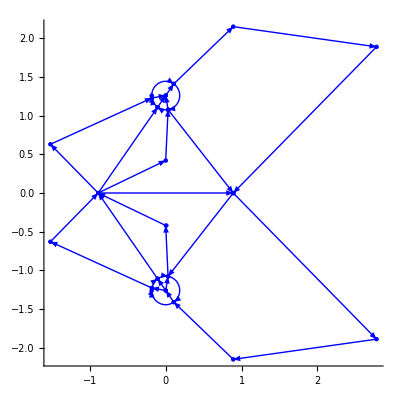

0.184688

1.25992

0.184688

```mathematica
tt=2000.;
wtest=wfun[0.,tt]
Show[{JumpsLittleCircles[wtest,tt]//DomainPlot}]
smallrad[wtest,tt]//N
Im[zsimplep[wtest]]//N
tt^(-2/9)//N
```

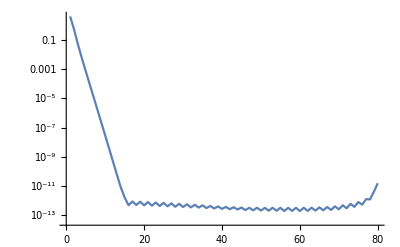
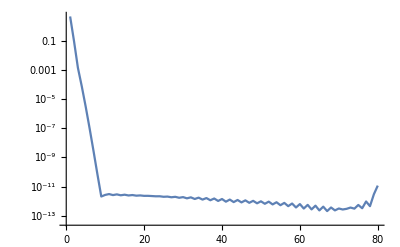
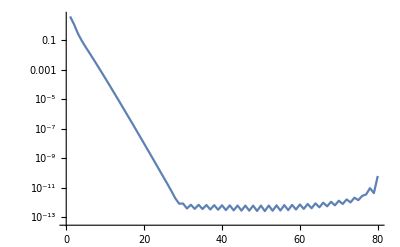
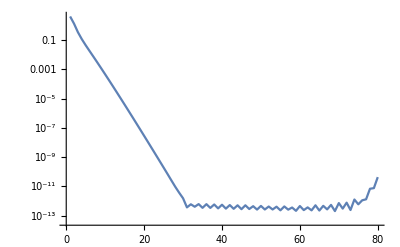
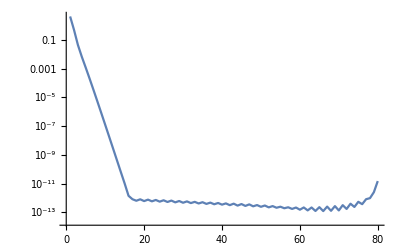
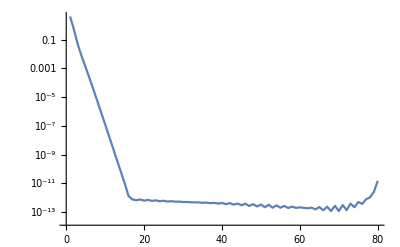
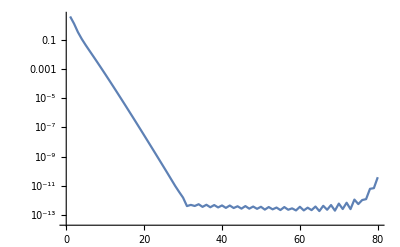
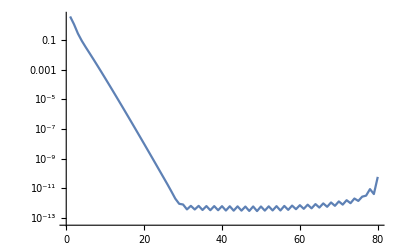

(Arc[0.+1.25992 ⅈ,0.171449,{-2.18628,-2.97167}]
Arc[0.+1.25992 ⅈ,0.171449,{-2.97167,-π}]
Arc[0.+1.25992 ⅈ,0.171449,{-π,-5.32787}]
Arc[0.+1.25992 ⅈ,0.171449,{0.955317,-1.40088}]
Arc[0.+1.25992 ⅈ,0.171449,{-1.40088,-2.18628}]
Arc[0.-1.25992 ⅈ,0.171449,{2.18628,1.40088}]
Arc[0.-1.25992 ⅈ,0.171449,{1.40088,-0.955317}]
Arc[0.-1.25992 ⅈ,0.171449,{-0.955317,-π}]
Arc[0.-1.25992 ⅈ,0.171449,{π,2.97167}]
Arc[0.-1.25992 ⅈ,0.171449,{2.97167,2.18628}]
Line[{-0.16898+1.23093 ⅈ,0.+1.25992 ⅈ}]
Line[{0.+1.25992 ⅈ,0.098986+1.39991 ⅈ}]
Line[{0.0289923+1.09094 ⅈ,0.+1.25992 ⅈ}]
Line[{-0.098986+1.11993 ⅈ,0.+1.25992 ⅈ}]
Line[{0.-1.25992 ⅈ,-0.098986-1.11993 ⅈ}]
Line[{0.-1.25992 ⅈ,0.0289923-1.09094 ⅈ}]
Line[{0.098986-1.39991 ⅈ,0.-1.25992 ⅈ}]
Line[{0.-1.25992 ⅈ,-0.16898-1.23093 ⅈ}]
Line[{-0.098986-1.11993 ⅈ,-0.890899}]
Line[{-0.890899,-0.098986+1.11993 ⅈ}]
Line[{-0.890899,-1.52086+0.629961 ⅈ}]
Line[{-1.52086+0.629961 ⅈ,-0.16898+1.23093 ⅈ}]
Line[{0.098986+1.39991 ⅈ,0.890899+2.15082 ⅈ}]
Line[{0.890899+2.15082 ⅈ,2.78078+1.88988 ⅈ}]
Line[{2.78078+1.88988 ⅈ,0.890899}]
Line[{0.890899,2.78078-1.88988 ⅈ}]
Line[{2.78078-1.88988 ⅈ,0.890899-2.15082 ⅈ}]
Line[{0.890899-2.15082 ⅈ,0.098986-1.39991 ⅈ}]
Line[{-0.890899,0.+0.419974 ⅈ}]
Line[{0.+0.419974 ⅈ,0.0289923+1.09094 ⅈ}]
Line[{0.0289923+1.09094 ⅈ,0.890899}]
Line[{0.890899,0.0289923-1.09094 ⅈ}]
Line[{0.0289923-1.09094 ⅈ,0.-0.419974 ⅈ}]
Line[{0.-0.419974 ⅈ,-0.890899}]
Line[{-0.16898-1.23093 ⅈ,-1.52086-0.629961 ⅈ}]
Line[{-1.52086-0.629961 ⅈ,-0.890899}]
Line[{-0.890899,0.890899}])

```mathematica
soltempT=RHSolved[JumpsLittleCircles[wtest,tt]];
DCTPlot/@soltempT
(Domain/@soltempT)//MatrixForm
```

## Asymptotic Formulae for large T, small 0≤ w<54^(1/3)

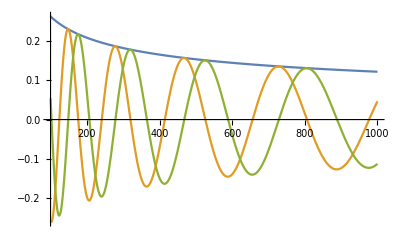

-0.00948151-0.0437463 ⅈ

```mathematica
expoTw0[T_]:=(108T)^(1/3)-Pi/2-(2/Pi)Log[2]ArcSinh[1/Sqrt[2]];
PsiAsympTw0[T_]:=(2/T)^(1/3)Exp[I(expoTw0[T])];

(***********)
p=Log[2]/(2Pi);
(*There were already defined in RHP computations. *)
LineSqrt[z0_,a_][z_]:=Sqrt[(z-z0)/(z-a)](z-a);
R[w_][z_]:=LineSqrt[zsimplep[w],adouble[w]][z]*LineSqrt[adouble[w],zsimplem[w]][z]/(z-adouble[w]);
(***********)
μ[w_]:=2p NIntegrate[1/Re[Rstd[w][x]],{x,adouble[w],bdouble[w]}];
expoT[w_,T_]:=-(T^(1/3)Re[κR[w]]+Re[μ[w]]);
PsiAsympT[w_,T_]:=-I(1/T)^(1/3)Im[zsimplep[w]]Exp[I(expoT[w,T])];

wtest=1;
Plot[{Abs[PsiAsympT[wtest,T]],Re[PsiAsympT[wtest,T]],Im[PsiAsympT[wtest,T]]},{T,100,1000},PlotRange->All]
PsiAsympT[wtest, 20000]
```

# COMPUTE SNAPSHOTS OF Ψ

```mathematica
dictPsiSnapshotAtT=<||>;
dictXdomAtT=<||>;
dictDomainPsiSnapshotAtT=<||>;
```

```mathematica
wfun[X_,T_]:=X/(T^(2/3));
vfun[X_,T_]:=T/X^((3/2));
dX=0.1;
dT=0.25;
Xend=10.;
Tend=2.;
Xdom0=Table[X,{X,0.,Xend,dX}];
(*Xcrit[T_]:=Round[wcrit*T^(2/3),dX/2];*)
Xcrit[T_]:=wcrit*T^(2/3);
Xcritorig[T_]:=Ceiling[wcrit*T^(2/3),dX]+dX;
times=Table[T,{T,0,Tend,dT}];
times[[1]]
Xcrit[0.2]
wcrit*0.2^(2/3)
(*Create the X-domain this way to avoid the transition region in the (X,T)-plane for now.*)
XlistRHPT[T_]:=Join[Table[-X,{X,-(Xcrit[T]-dX/2),-0,dX}],{0.}]//Reverse//Union;
XlistRHPX[T_]:=Join[Table[X,{X,(Xcrit[T]+dX/2),Xend,dX}],{Xend}]//Union;
XlistRHPorig[T_]:=Select[Xdom0,#≤Xcritorig[T]&];
XlistRHPXForOrig[T_]:=Select[Xdom0,#>Xcritorig[T]&];

PsiSnapshotAtT[TT_]:=Module[{nlSTableAtTFromRHPT,nlSTableAtTFromRHPX},
nlSTableAtTFromRHPT=Monitor[nlsLittleCirclesT[wfun[#,TT],#]&/@XlistRHPT[TT],TT];
nlSTableAtTFromRHPX=Monitor[nlsLinesX[#,vfun[#,TT]]&/@XlistRHPX[TT],TT];
Return[{Join[XlistRHPT[TT],XlistRHPX[TT]],Join[nlSTableAtTFromRHPT,nlSTableAtTFromRHPX]}];
];
PsiSnapshotAtTNoDeform[TT_]:=Module[{nlSTableAtTFromRHPT,nlSTableAtTFromRHPX},
nlSTableAtTFromRHPT=(nlsOrig[circrad][#,TT]&/@XlistRHPorig[TT]);
nlSTableAtTFromRHPX=(nlsTruncLinesCirclesX[#,vfun[#,TT]]&/@XlistRHPXForOrig[TT]);
Return[{Join[XlistRHPorig[TT],XlistRHPXForOrig[TT]],Join[nlSTableAtTFromRHPT,nlSTableAtTFromRHPX]}];
];
ComputePsiSnapshotAndAppend[dict_][TT_]:=Module[{},
dict=Append[dict,TT->PsiSnapshotAtTNoDeform[TT]];
];
```

```mathematica
(*Treat T=0 separately using the Large-X problem only.*)
nlsTableAtT0=Monitor[Table[nlsLinesCirclesXv0[X],{X,0.,Xend,dX}],X];
Append[dictDomainPsiSnapshotAtT,0.->nlsTableatT0]
```

```mathematica
Do[
Clear[nlsDomRHPTableAtT];
tt=0.+idt*dT;
nlsDomRHPTableAtT=PsiSnapshotAtTNoDeform[tt],{idt,1,20};
dictDomainPsiSnapshotAtT=Append[dictDomainPsiSnapshotAtT,tt->nlsDomRHPTableAtT];
dictDomainPsiSnapshotAtT>>"dictDomainAndPsiSnapshotTable-put.m"
]
```

```mathematica
dictDomainPsiSnapshotAtT>>"dictDomainAndPsiSnapshotTable-put.m"
```

```mathematica
TT=0.;
Clear[RePsiFun];Clear[ImPsiFun]
RePsiFunInt=Interpolation[Transpose@{dictXdomAtT[TT],Re[dictPsiSnapshotAtT[TT]]}]
RePsiFun[X_]:=Piecewise[{{RePsiFunInt[X],X≥0},{RePsiFunInt[-X],X<0}}];
ImPsiFunInt=Interpolation[Transpose@{dictXdomAtT[TT],Im[dictPsiSnapshotAtT[TT]]}]
ImPsiFun[X_]:=Piecewise[{{ImPsiFunInt[X],X≥0},{ImPsiFunInt[-X],X<0}}];
```

InterpolatingFunction[{{0., 10.}}, <>]

InterpolatingFunction[{{0., 10.}}, <>]

```mathematica
tt=0.05;
```

```mathematica
Clear[nlsDomRHPTableAtT];
```

```mathematica
nlsDomRHPTableAtT=PsiSnapshotAtTNoDeform[tt];
```

```mathematica
RePsiFunIntAtT0p25=
Interpolation[Transpose@{nlsDomRHPTableAtT[[1]],Re[nlsDomRHPTableAtT[[2]]]}];
RePsiFunAtT0p25[X_]:=Piecewise[{{RePsiFunIntAtT0p25[X],X≥0},{RePsiFunIntAtT0p25[-X],X<0}}];
ImPsiFunIntAtT0p25=Interpolation[Transpose@{nlsDomRHPTableAtT[[1]],Im[nlsDomRHPTableAtT[[2]]]}];
ImPsiFunAtT0p25[X_]:=Piecewise[{{ImPsiFunIntAtT0p25[X],X≥0},{ImPsiFunIntAtT0p25[-X],X<0}}];
```

```mathematica
soltempX=RHSolved[JumpsLinesX[XlistRHPX[tt][[1]],vfun[XlistRHPX[tt][[1]],tt]]];
DCTPlot/@soltempX
(Domain/@soltempX)//MatrixForm
```

RHSolve[DCTPlot[JumpsLinesX[2.,0.707107]]]

RHSolve[Domain[JumpsLinesX[2.,0.707107]]]

```mathematica
vfun[XlistRHPX[tt][[1]],tt]
1/Sqrt[54]//N
```

0.123526

0.136083

## Compute LogLog Plots

```mathematica
Xtable=Table[2000+10k,{k,1,60}]
```

{2010,2020,2030,2040,2050,2060,2070,2080,2090,2100,2110,2120,2130,2140,2150,2160,2170,2180,2190,2200,2210,2220,2230,2240,2250,2260,2270,2280,2290,2300,2310,2320,2330,2340,2350,2360,2370,2380,2390,2400,2410,2420,2430,2440,2450,2460,2470,2480,2490,2500,2510,2520,2530,2540,2550,2560,2570,2580,2590,2600}

```mathematica
(*nlsLargeXtable=Map[nlsTruncLinesXv0,Xtable]//Chop;*)
nlsLargeXtable=Map[nlsLinesCirclesX[#,0.]&, Xtable]//Chop;
asympLargeXtable=Map[PsiAsympXv0[#]&,Xtable]//Chop;
LogLogLargeXerror=Transpose@{Log[Xtable],Log[Abs[nlsLargeXtable-asympLargeXtable]]};
```

-5.40862-1.01184 t

| Estimate | Standard Error | t-Statistic | P-Value
1 | -5.40862 | 9.72732 | -0.556024 | 0.580333
t | -1.01184 | 1.2567 | -0.805158 | 0.424017

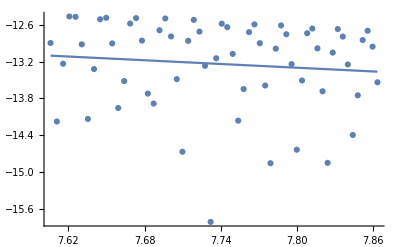

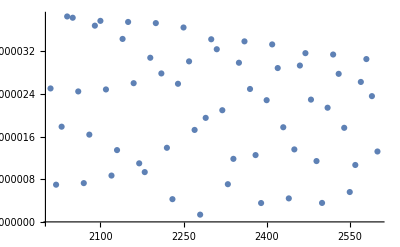

```mathematica
modelLargeX=LinearModelFit[LogLogLargeXerror,τ,τ];
modelLargeX["BestFit"]
modelLargeX["ParameterTable"]
Show[ListPlot[LogLogLargeXerror],Plot[modelLargeX[t],{t,Log[Xtable[[1]]],Log[Xtable[[-1]]]}]]
ListPlot[Transpose@{Xtable,Abs[nlsLargeXtable-asympLargeXtable]}]
```

```mathematica
RHOrigSol[circrad][0.,3.]//Chop
```

{{-4.,0.204729-0.938757 ⅈ},{0.204729+0.938757 ⅈ,4.}}

```mathematica
Xtable2=Table[2(100+20(k-1)),{k,1,41}]
```

{200,240,280,320,360,400,440,480,520,560,600,640,680,720,760,800,840,880,920,960,1000,1040,1080,1120,1160,1200,1240,1280,1320,1360,1400,1440,1480,1520,1560,1600,1640,1680,1720,1760,1800}

```mathematica
nlsLargeXtable=Map[nlsLinesCirclesX[#,0.]&, Xtable2]//Chop;
asympLargeXtable=Map[PsiAsympXv0[#]&,Xtable2]//Chop;
LogLogLargeXerror=Transpose@{Log[Xtable2],Log[Abs[nlsLargeXtable-asympLargeXtable]]};
```

```mathematica
LogLogLargeXerror>>"datafor-largeX-LogLogError-plot-X200to1800-dX40.m"
```

-4.82864-1.05592 τ

| Estimate | Standard Error | t-Statistic | P-Value
1 | -4.82864 | 1.41996 | -3.40054 | 0.00156453
τ | -1.05592 | 0.209238 | -5.04652 | 0.0000108132

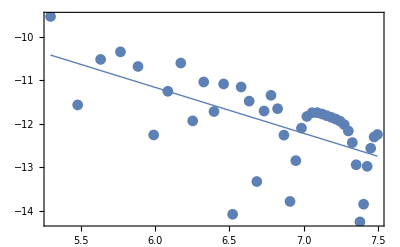

```mathematica
modelLargeX=LinearModelFit[LogLogLargeXerror,τ,τ];
modelLargeX["BestFit"]
modelLargeX["ParameterTable"]
Show[ListPlot[LogLogLargeXerror,PlotMarkers->circle[]],Plot[modelLargeX[t],{t,Log[Xtable2[[1]]],Log[Xtable2[[-1]]]},PlotStyle->Thick],Frame->True]
```